# Active Learning - Continuous

## Set Up & Helper Functions

Define the vectors denoting the concentrations of each reagent in the form {lead nitrate concentration, potassium iodide concentration}

```mathematica
leadStock={0.01,0}; (*example lab used 0.01 M solutions for each; lead nitrate and KI*)
iodineStock={0.0,0.01};
water={0,0};
ch=ConvexHullMesh[{leadStock,iodineStock,water}];

Ksp = 1.4*10^(-8); (*equilibrium constant found on the internet*)
```

The equation for lead iodide precipitation is as follows along with its subsequent Ksp equation:
PbI_2 ↔ Pb^(2+)(aq) + 2I^-(aq) ; K_sp = ([Pb^(2+)][I^-])^2
To make judgements on whether or not precipitation occurs, we would generally compare K_sp to the value of Q, the reaction quotient. If Q ≥ K → ppt, if Q < K, no ppt. Taking Q to be (Pb^(2+))(I^-)^2 where each concentration are not equilibrium values, we can derive a condition for precipitation:

ppt. occurs if Q ≥ K_sp  
ppt. occurs if (Pb^(2+))(I^-)^2 ≥ K_sp
ppt. occurs if (I^-) ≥ √K_sp/(Pb^(2+)) -- which is the form of the following function, pbI2Precipitates[]. This yields boolean values.

```mathematica
pbI2Precipitates[{Pb_,Iodine_},Ksp_:1.4*10^-8]:=(Iodine>=Sqrt[Ksp/Pb])
```

```mathematica
pbI2Precipitates[{Pb_,Iodine_},Ksp_:1.4*10^-8]:=If[Pb==0,False,(Iodine>=Sqrt[Ksp/Pb])]
```

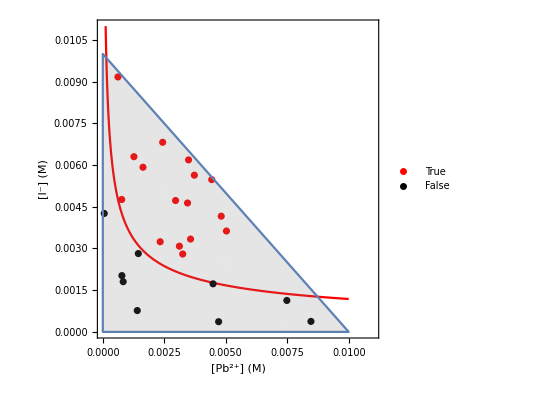

```mathematica
sdPlot2D=Show[Plot[Sqrt[Ksp/Pb],{Pb,10^-5,0.01},PlotRange->{{0,0.011},{0,0.011}},PlotStyle->Red,AspectRatio->1,Frame->True,FrameLabel->{"[Pb^(2+)] (M)","[I^-] (M)"}],ListPlot[{Select[Thread[{Normal[startDat],pbI2Precipitates/@Normal[startDat]}],Last[#]&][[All,1]],Select[Thread[{Normal[startDat],pbI2Precipitates/@Normal[startDat]}],Not@Last[#]&][[All,1]]},PlotStyle->{Red,Black},PlotLegends->Placed[{"True","False"},{0.9,0.9}]],
RegionPlot[ch,PlotStyle->{Gray,Opacity[0.2]}],LabelStyle->Black]
```

```mathematica
Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\stDatPlot2D.pdf",sdPlot2D,"PDF"];
```

```mathematica
RandomSeed[1997];
pts350=RandomPoint[ch,350];
```

```mathematica
(* held out 75 point test set *)
```

```mathematica
(*allTrain,test}=ResourceFunction["TrainTestSplit"][pts350,"TestSetSize"->75];
```

```mathematica
(*{startDat,pool}=ResourceFunction["TrainTestSplit"][allTrain,"TestSetSize"->250];
```

```mathematica
test=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\testCont.csv"];
pool=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\poolCont.csv"];
startDat=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\startDatCont.csv"];
```

```mathematica
startDat5=Normal[startDat[[1;;5]]];
```

```mathematica
(* start with 25 initial points, pool up to 250 *)
```

```mathematica
Length@startDat
Length@pool
```

25

250

```mathematica
noisyOracle[data_,noisePercent_]:=Module[{swap,thread},
swap=Flatten[Table[RandomSample[{noisePercent,1-noisePercent}->{-1,1},1],Length[data]]];(* assign a value {-1,+1} to each example in data given some probability *)
thread=Thread[{(pbI2Precipitates/@Normal[data]),swap}];(* thread each ex's class and the random value *)
Which[
#[[2]]==1,(* if the random value is 1 --> *)
#[[1]], (* keep class same *)
#[[2]]==-1,(* if random value is -1 --> *)
Not[#[[1]]](* swap class boolean *)
]&/@thread
]
```

```mathematica
avgAcc[dat_]:=Table[Total[Normal[dat[[j]][All,"Accuracy"]]]/Length[dat[[j]]],{j,1,Length[dat]}]
```

```mathematica
maxAcc[dat_]:=Table[Max[Normal[dat[[j]][All,"Accuracy"]]],{j,1,Length[dat]}]
```

```mathematica
maxMCC[dat_]:=Table[Max[Normal[dat[[j]][All,"MatthewsCorrelationCoefficient"]]],{j,1,Length[dat]}]/.Indeterminate->0
```

```mathematica
maxAccPos[dat_]:=Flatten[Table[First@Position[Normal[dat[[j]][All,"Accuracy"]],Max[Normal[dat[[j]][All,"Accuracy"]]]],{j,1,Length[dat]}]]
```

```mathematica
maxMCCPos[dat_]:=Select[Flatten[Table[First@Position[Normal[dat[[j]][All,"MatthewsCorrelationCoefficient"]],Max[Normal[dat[[j]][All,"MatthewsCorrelationCoefficient"]]]],{j,1,Length[dat]}]],NumberQ[#]&]
```

### Imbalanced Data

```mathematica
(* let's change Ksp to make this more imbalanced *)
```

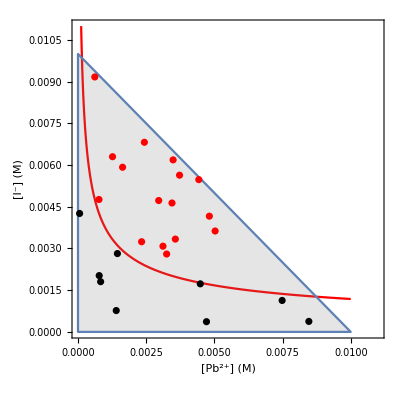

```mathematica
Show[Plot[Sqrt[Ksp/Pb],{Pb,10^-5,0.01},PlotRange->{{0,0.011},{0,0.011}},PlotStyle->Red,AspectRatio->1,Frame->True,FrameLabel->{"[Pb^(2+)] (M)","[I^-] (M)"}],
RegionPlot[ch,PlotStyle->{Gray,Opacity[0.2]}],ListPlot[ {Select[startDat,pbI2Precipitates],Select[startDat,Not@pbI2Precipitates[#]&]},PlotStyle->{Red,Black}]]
```

```mathematica
(* now we'll have an imbalanced space to explore *)
```

```mathematica
kspImb=5*10^-8;
```

```mathematica
pbI2ImbPrecipitates[{Pb_,Iodine_},Ksp_:kspImb]:=(Iodine>=Sqrt[Ksp/Pb])
```

```mathematica
pbI2ImbPrecipitates[{Pb_,Iodine_},Ksp_:kspImb]:=If[Pb==0,False,(Iodine>=Sqrt[Ksp/Pb])]
```

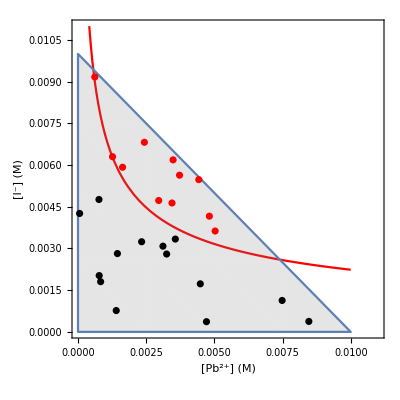

```mathematica
Show[Plot[Sqrt[kspImb/Pb],{Pb,10^-5,0.01},PlotRange->{{0,0.011},{0,0.011}},PlotStyle->Red,AspectRatio->1,Frame->True,FrameLabel->{"[Pb^(2+)] (M)","[I^-] (M)"}],
RegionPlot[ch,PlotStyle->{Gray,Opacity[0.2]}],ListPlot[ {Select[startDat,pbI2ImbPrecipitates],Select[startDat,Not@pbI2ImbPrecipitates[#]&]},PlotStyle->{Red,Black}]]
```

## Initial Classifier Train

```mathematica
(*clfInit=Classify[startDat->(pbI2Precipitates/@startDat),Method->"SupportVectorMachine"]
```

```mathematica
(*clfInit10pc=Classify[startDat->noisyOracle[startDat,0.1],Method->"SupportVectorMachine"]
```

```mathematica
(*clfInit20pc=Classify[startDat->noisyOracle[startDat,0.2],Method->"SupportVectorMachine"]
```

```mathematica
(*clfInit30pc=Classify[startDat->noisyOracle[startDat,0.3],Method->"SupportVectorMachine"]
```

```mathematica
(*clfInit40pc=Classify[startDat->noisyOracle[startDat,0.4],Method->"SupportVectorMachine"]
```

```mathematica
(*clfInit50pc=Classify[startDat->noisyOracle[startDat,0.5],Method->"SupportVectorMachine"]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit.wmlf",clfInit,"WMLF"];
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit10pc.wmlf",clfInit10pc,"WMLF"];
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit20pc.wmlf",clfInit20pc,"WMLF"];
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit30pc.wmlf",clfInit30pc,"WMLF"];
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit40pc.wmlf",clfInit40pc,"WMLF"];
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit50pc.wmlf",clfInit50pc,"WMLF"];
```

```mathematica
clfInit5=Classify[Normal[startDat[[1;;5]]]->pbI2ImbPrecipitates/@Normal[startDat[[1;;5]]],Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
clfInit=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit.wmlf"];
clfInit10pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit10pc.wmlf"];
clfInit20pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit20pc.wmlf"];
clfInit30pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit30pc.wmlf"];
clfInit40pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit40pc.wmlf"];
clfInit50pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit50pc.wmlf"];
```

```mathematica
clfNs={clfInit10pc,clfInit20pc,clfInit30pc,clfInit40pc,clfInit50pc};
```

```mathematica
(*{clfInit10pc5,clfInit20pc5,clfInit30pc5,clfInit40pc5,clfInit50pc5}=Table[Classify[startDat5->noisyOracle[startDat5,noisePCs[[l]]],Method->"SupportVectorMachine"],{l,1,Length@noisePCs}];
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit50pc5.wmlf",clfInit50pc5,"WMLF"];
```

```mathematica
clfInit10pc5=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit10pc5.wmlf"];
clfInit20pc5=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit20pc5.wmlf"];
clfInit30pc5=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit30pc5.wmlf"];
clfInit40pc5=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit40pc5.wmlf"];
clfInit50pc5=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInit50pc5.wmlf"];
```

```mathematica
clfNs5={clfInit10pc5,clfInit20pc5,clfInit30pc5,clfInit40pc5,clfInit50pc5};
```

### Imbalanced Data

```mathematica
(*clfInitImb=Classify[startDat->(pbI2ImbPrecipitates/@startDat),Method->"SupportVectorMachine"]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInitImb.wmlf",clfInitImb,"WMLF"];
```

```mathematica
clfInitImb=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\clfInitImb.wmlf"];
```

### Analysis

```mathematica
(* how does this initial classifier do? *)
```

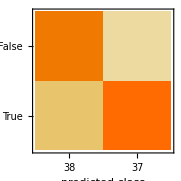
Classifier Measurements
Classifier method | SupportVectorMachine
Number of test examples | 75
Accuracy | (84.4.) %
Accuracy baseline | (52.6.) %
Geometric mean of probabilities | 0.749 ± 0.053
Mean cross entropy | 0.289 ± 0.071
Single evaluation time | 3.04 ms/example
Batch evaluation speed | 9.34 examples/ms
-Graphics- |

```mathematica
clfInitMeas=ClassifierMeasurements[clfInit,test->(pbI2Precipitates/@test)]
```

```mathematica
{clfInit10pcMeas,clfInit20pcMeas,clfInit30pcMeas,clfInit40pcMeas,clfInit50pcMeas}=Table[ClassifierMeasurements[clfNs[[l]],test->(pbI2Precipitates/@test)],{l,1,Length@clfNs}];
```

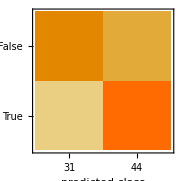
Classifier Measurements
Classifier method | SupportVectorMachine
Number of test examples | 75
Accuracy | (67.5.) %
Accuracy baseline | (52.6.) %
Geometric mean of probabilities | 0.495 ± 0.05
Mean cross entropy | 0.704 ± 0.1
Single evaluation time | 3.14 ms/example
Batch evaluation speed | 8.19 examples/ms
-Graphics- |

```mathematica
clfInit5Meas=ClassifierMeasurements[clfInit5,test->(pbI2Precipitates/@test)]
```

## Grid Search - done

### Analyze Timings

```mathematica
numIts=150;(* AL iterations *)
numReps=5;(* simulation replications *)
```

```mathematica
(* using a While[] loop with AppendTo[] *)
```

```mathematica
(*AbsoluteTiming[Table[
Clear[clfsGS,tDatGS,classif,newDat,tPool,i,newPt];
clfsGS={};
tDatGS={};
classif=clfInit;
tPool=tGrid;
newDat=startDat;
i=1;
While[i<=5,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
AppendTo[clfsGS,classif];
AppendTo[tDatGS,newDat];
i++
];
{clfsGS,tDatGS},
{j,1,numReps}];]
```

{16.0914,Null}

```mathematica
(* using a While[] loop with AppendTo[] and Classify goal --> speed *)
```

```mathematica
(*AbsoluteTiming[Table[
Clear[clfsGS,tDatGS,classif,newDat,tPool,i,newPt];
clfsGS={};
tDatGS={};
classif=clfInit;
tPool=tGrid;
newDat=startDat;
i=1;
While[i<=5,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS,classif];
AppendTo[tDatGS,newDat];
i++
];
{clfsGS,tDatGS},
{j,1,numReps}];]
```

{9.70176,Null}

```mathematica
(* using While[] loop with Sow[] and Reap[]
```

```mathematica
(*AbsoluteTiming[Table[
Clear[clfsGS,tDatGS,classif,newDat,tPool,i,newPt];
classif=clfInit;
newDat=startDat;
tPool=tGrid;
i=1;
Reap[While[i<=5,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
{Sow[classif],Sow[newDat]};
i++
]],
{j,1,numReps}];]
```

{16.1676,Null}

```mathematica
(* using While[] loop with Sow[] and Reap[] and Classifier performance --> speed *)
```

```mathematica
(*AbsoluteTiming[Table[
Clear[clfsGS,tDatGS,classif,newDat,tPool,i,newPt];
classif=clfInit;
newDat=startDat;
tPool=tGrid;
i=1;
Reap[While[i<=5,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
{Sow[classif],Sow[newDat]};
i++
]],
{j,1,numReps}];]
```

{9.75233,Null}

```mathematica
(* using Table[] instead of While[] *)
```

```mathematica
(*AbsoluteTiming[out=Table[
Clear[clfsGS,tDatGS,classif,newDat,tPool,i,newPt];
classif=clfInit;
newDat=startDat;
tPool=tGrid;
Flatten[Table[
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
{classif,newDat}
,{i,1,5}],1],
{j,1,numReps}];]
```

{16.4621,Null}

```mathematica
(* using Table[] instead of While[] and performance --> speed *)
```

```mathematica
(*AbsoluteTiming[out=Table[
Clear[clfsGS,tDatGS,classif,newDat,tPool,i,newPt];
classif=clfInit;
newDat=startDat;
tPool=tGrid;
Flatten[Table[
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
{classif,newDat}
,{i,1,5}],1],
{j,1,numReps}];]
```

{9.79861,Null}

### Define the grid

```mathematica
Clear[addDrop]
addDrop[conc2_,v2_][{conc_,vol_}]:=addDrop[conc,vol,conc2,v2]

addDrop[conc_,vol_,conc2_,v2_]:=With[
{vf=vol/(vol+v2)},
{conc*vf+conc2*(1-vf),vol+v2}]

addDrop[_,0,_,0]:={{0.,0.},0}
```

```mathematica
(* tGrid is whatever temp grid w/ however many grid pts we want *)
```

```mathematica
gstGrid=Partition[#,2]&@Flatten@Table[
If[ x+y+z==13,
First@addDrop[leadStock,x]@addDrop[iodineStock,y][{water,z}],
Nothing],
{x,0,30},{y,0,30},{z,0,30}];
Length@gstGrid
```

105

```mathematica
(* how many grid lines - including x and y axes *)
```

```mathematica
DeleteDuplicates[tGrid[[All,1]]]//Length
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

```mathematica
(* plot the grid points *)
```

```mathematica
$PlotTheme->Scientific
```

Automatic→Scientific

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\gridDat2D.csv",gstGrid];
```

### Simulations - Noiseless

Run the grid search simulation in replicate 5 times.

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGS,tDatGS,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[gsSims=Table[
Clear[clfsGS,tDatGS,classif,newDat,tPool,i,newPt];
clfsGS={};
tDatGS={};
classif=clfInit;
newDat=Normal[startDat];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS,classif];
AppendTo[tDatGS,newDat];
i++
];
{clfsGS,tDatGS},
{j,1,numReps}];]
```

{168.238,Null}

### Simulations - Noiseless, starting from 5

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGS5,tDatGS5,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[gsSims5=Table[
Clear[clfsGS5,tDatGS5,classif,newDat,tPool,i,newPt];
clfsGS5={};
tDatGS5={};
classif=clfInit5;
newDat=Normal[startDat[[1;;5]]];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS5,classif];
AppendTo[tDatGS5,newDat];
i++
];
{clfsGS5,tDatGS5},
{j,1,numReps}];]
```

TakeDrop::iseq: Invalid sequence specification {54} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{54}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {55} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{55}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {56} for an expression of length 52.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{56}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{150.878,Null}

### Simulations - Noise

#### 10% Noise

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Length@gstGrid
```

105

```mathematica
(*AbsoluteTiming[gsSims10pc=Table[
Clear[clfsGS10pc,tDatGS10pc,classif,newDat,tPool,i,newPt];
clfsGS10pc={};
tDatGS10pc={};
classif=clfInit10pc;
newDat=Normal[startDat];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,0.1],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS10pc,classif];
AppendTo[tDatGS10pc,newDat];
i++
];
{clfsGS10pc,tDatGS10pc},
{j,1,numReps}];]
```

{174.269,Null}

#### 20% Noise

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Length@gstGrid
```

105

```mathematica
(*AbsoluteTiming[gsSims20pc=Table[
Clear[clfsGS20pc,tDatGS20pc,classif,newDat,tPool,i,newPt];
clfsGS20pc={};
tDatGS20pc={};
classif=clfInit20pc;
newDat=Normal[startDat];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,0.2],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS20pc,classif];
AppendTo[tDatGS20pc,newDat];
i++
];
{clfsGS20pc,tDatGS20pc},
{j,1,numReps}];]
```

{177.232,Null}

#### 30% Noise

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Length@gstGrid
```

105

```mathematica
(*AbsoluteTiming[gsSims30pc=Table[
Clear[clfsGS30pc,tDatGS30pc,classif,newDat,tPool,i,newPt];
clfsGS30pc={};
tDatGS30pc={};
classif=clfInit30pc;
newDat=Normal[startDat];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,0.3],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS30pc,classif];
AppendTo[tDatGS30pc,newDat];
i++
];
{clfsGS30pc,tDatGS30pc},
{j,1,numReps}];]
```

{176.155,Null}

#### 40% Noise

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Length@gstGrid
```

105

```mathematica
(*AbsoluteTiming[gsSims40pc=Table[
Clear[clfsGS40pc,tDatGS40pc,classif,newDat,tPool,i,newPt];
clfsGS40pc={};
tDatGS40pc={};
classif=clfInit40pc;
newDat=Normal[startDat];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,0.4],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS40pc,classif];
AppendTo[tDatGS40pc,newDat];
i++
];
{clfsGS40pc,tDatGS40pc},
{j,1,numReps}];]
```

TakeDrop::iseq: Invalid sequence specification {54} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{54}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {55} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{55}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {56} for an expression of length 52.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{56}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{174.859,Null}

#### 50% Noise

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Length@gstGrid
```

105

```mathematica
(*AbsoluteTiming[gsSims50pc=Table[
Clear[clfsGS50pc,tDatGS50pc,classif,newDat,tPool,i,newPt];
clfsGS50pc={};
tDatGS50pc={};
classif=clfInit50pc;
newDat=Normal[startDat];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,0.5],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS50pc,classif];
AppendTo[tDatGS50pc,newDat];
i++
];
{clfsGS50pc,tDatGS50pc},
{j,1,numReps}];]
```

TakeDrop::iseq: Invalid sequence specification {54} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{54}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {55} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{55}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {56} for an expression of length 52.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{56}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{164.909,Null}

### Simulations - noise, start from 5

Run the grid search simulation in replicate 5 times.

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGS,tDatGS,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[{gsSims10pc5,gsSims20pc5,gsSims30pc5,gsSims40pc5,gsSims50pc5}=Table[Table[
Clear[clfsGSn5,tDatGSn5,classif,newDat,tPool,i,newPt];
clfsGSn5={};
tDatGSn5={};
classif=clfNs5[[l]];
newDat=Normal[startDat5];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGSn5,classif];
AppendTo[tDatGSn5,newDat];
i++
];
{clfsGSn5,tDatGSn5},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

TakeDrop::iseq: Invalid sequence specification {54} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{54}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {55} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{55}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {56} for an expression of length 52.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.000769231},{0.,0.00230769},{0.,0.00384615},{0.,0.00538462},{0.,0.00692308},{0.,0.00846154},{0.,0.01},{0.000769231,0.000769231},{0.000769231,0.00230769},{0.000769231,0.00384615},«42»},{56}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Classify::mincnb: The dataset should contain at least two different classes.

{783.794,Null}

### Simulations - Imbalanced

```mathematica
(* w/ 100 its and 5 reps and normal performance goal it took 438 s *)
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGSImb,tDatGSImb,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[gsSimsImb=Table[
Clear[clfsGSImb,tDatGSImb,classif,newDat,tPool,i,newPt];
clfsGSImb={};
tDatGSImb={};
classif=clfInitImb;
newDat=Normal[startDat];
tPool=gstGrid;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2ImbPrecipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGSImb,classif];
AppendTo[tDatGSImb,newDat];
i++
];
{clfsGSImb,tDatGSImb},
{j,1,numReps}];]
```

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gsClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gsClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gsClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gsClfs=Partition[Map[Import[#]&,gsClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gsSims[[All,1]];*)
clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gsClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gsRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGSmeas];
```

### Analysis - Noiseless, start from 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs5Clfs=Partition[Map[Import[#]&,gs5ClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gsSims[[All,1]];*)
clfGS5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS5meas];
```

### Analysis - Noise

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs10pcClfs=Partition[Map[Import[#]&,gs10pcClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs10pcSims[[All,1]];*)
clfGS10pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS10pcmeas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs20pcClfs=Partition[Map[Import[#]&,gs20pcClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs20pcSims[[All,1]];*)
clfGS20pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS20pcmeas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs30pcClfs=Partition[Map[Import[#]&,gs30pcClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs30pcSims[[All,1]];*)
clfGS30pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS30pcmeas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs40pcClfs=Partition[Map[Import[#]&,gs40pcClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs40pcSims[[All,1]];*)
clfGS40pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS40pcmeas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs50pcClfs=Partition[Map[Import[#]&,gs50pcClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs50pcSims[[All,1]];*)
clfGS50pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS50pcmeas];
```

### Analysis - Noise, start from 5

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs10pc5Clfs=Partition[Map[Import[#]&,gs10pc5ClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs10pcSims[[All,1]];*)
clfGS10pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS10pc5meas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs20pc5Clfs=Partition[Map[Import[#]&,gs20pc5ClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs20pcSims[[All,1]];*)
clfGS20pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS20pc5meas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs30pc5Clfs=Partition[Map[Import[#]&,gs30pc5ClfPaths],numIts];
```

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs30pcSims[[All,1]];*)
clfGS30pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS30pc5meas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs40pc5Clfs=Partition[Map[Import[#]&,gs40pc5ClfPaths],numIts];
```

Classify::mincnb: The dataset should contain at least two different classes.

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs40pcSims[[All,1]];*)
clfGS40pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs40pc5Clfs;
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Classify[{{0.00846469,0.000376962},{0.00295948,0.00472605},{0.0016345,0.0059227},{0.00471039,0.00036683},{0.0024342,0.00682089},{0.,0.}}→{False,False,False,False,False,False},Method→SupportVectorMachine,TrainingProgressReporting→None,PerformanceGoal→TrainingSpeed].

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS40pc5meas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs50pc5Clfs=Partition[Map[Import[#]&,gs50pc5ClfPaths],numIts];
```

Classify::mincnb: The dataset should contain at least two different classes.

```mathematica
(*clfGSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs50pcSims[[All,1]];*)
clfGS50pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@gs50pc5Clfs;
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Classify[{{0.00846469,0.000376962},{0.00295948,0.00472605},{0.0016345,0.0059227},{0.00471039,0.00036683},{0.0024342,0.00682089},{0.,0.},{0.,0.00153846}}→{True,True,True,True,True,True,True},Method→SupportVectorMachine,TrainingProgressReporting→None,PerformanceGoal→TrainingSpeed].

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS50pc5meas];
```

### Analysis - Imbalanced

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gsImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSimsImb[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gsImbClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gsImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gsImbClfs=Partition[Map[Import[#]&,gsImbClfPaths],numIts];
```

```mathematica
(*clfGSImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@gsImbSims[[All,1]];*)
clfGSImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@gsImbClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gsImbRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGSImbmeas];
```

## Serial Dilution Rays - Line by Line - done

### Code up the ray points

```mathematica
Clear[addDrop]
addDrop[conc2_,v2_][{conc_,vol_}]:=addDrop[conc,vol,conc2,v2]

addDrop[conc_,vol_,conc2_,v2_]:=With[
{vf=vol/(vol+v2)},
{conc*vf+conc2*(1-vf),vol+v2}]

addDrop[_,0,_,0]:={{0.,0.},0}
```

```mathematica
(* tGrid is whatever temp grid w/ however many grid pts we want *)
```

```mathematica
tGrid=Partition[#,2]&@Flatten@Table[
If[ x+y+z==11,
First@addDrop[leadStock,x]@addDrop[iodineStock,y][{water,z}],
Nothing],
{x,0,11},{y,0,11},{z,0,11}];
```

```mathematica
(* how many grid lines - including x and y axes *)
```

```mathematica
DeleteDuplicates[tGrid[[All,1]]]//Length
```

12

```mathematica
(* plot the grid points *)
```

```mathematica
ListPlot@tGrid;
```

```mathematica
Length@tGrid
```

78

```mathematica
xs=DeleteDuplicates[tGrid[[All,1]]];(* all non-duplicate x values *)
```

```mathematica
Length@xs
```

12

```mathematica
ys=Table[Max[Select[tGrid,#[[1]]==xs[[i]]&][[All,2]]],{i,1,Length@xs}];(*max y vals corresponding to xs *)
```

```mathematica
upBound=Thread[{xs,ys}];(* coordinates of the upper bound line*)
```

```mathematica
Length@upBound
```

12

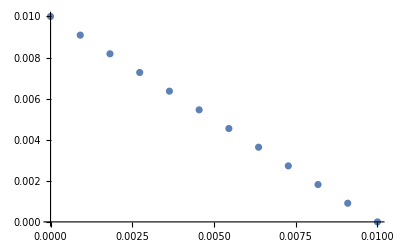

```mathematica
ListPlot@upBound
```

ListPlot::lpn: poolGrid is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[poolGrid]].

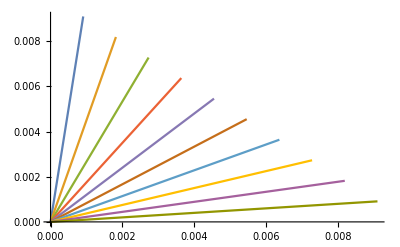
Show[-Graphics-,ListPlot[poolGrid]]

```mathematica
Show[ListLinePlot[{{0,0},#}&/@upBound[[2;;-2;;1]]],ListPlot@poolGrid]
```

```mathematica
(* defines the line given two points and outputs the y given an x *)
```

```mathematica
getLine[{x1:0,y1:0},{x2_,y2_},x_]:=Module[{m,b=0},
m=((y2-y1)/(x2-x1));
m*x+b
]
```

```mathematica
(* let's generate the data points now to make things faster *)
```

```mathematica
(* this is a nested list of {{boundPts}, {list of x's to be evaluated}}
```

```mathematica
ptXs=Thread[{upBound[[2;;-2;;1]],Rest[Range[0,#[[1]],#[[1]]/10]]&/@upBound[[2;;-2;;1]]}];
```

```mathematica
rayPts=Table[Thread[{ptXs[[j,2]],Table[getLine[{0,0},ptXs[[i]][[1]],#]&/@ptXs[[i]][[2]],{i,1,Length@ptXs}][[j]]}],{j,1,Length@ptXs}];
```

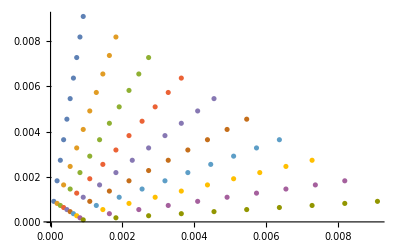

```mathematica
ListPlot@rayPts
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\rayPts2D.csv",Flatten[rayPts,1]];
```

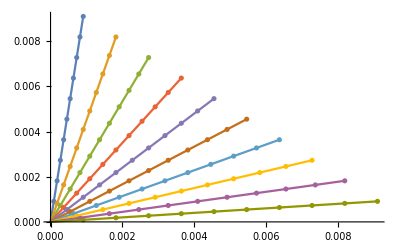

```mathematica
Show[ListPlot@rayPts,ListLinePlot[{{0,0},#}&/@upBound[[2;;-2;;1]]]]
```

```mathematica
Flatten[rayPts,1]//Length
```

100

### Simulations - Noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[rdSims=Table[
Clear[clfsRD,tDatRD,classif,newDat,tPool,i,newPt];
clfsRD={};
tDatRD={};
classif=clfInit;
newDat=startDat;
tPool=Flatten[rayPts,1];
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRD,classif];
AppendTo[tDatRD,newDat];
i++
];
{clfsRD,tDatRD},
{j,1,numReps}];]
```

{176.324,Null}

### Simulations - Noiseless, starting from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[rdSims5=Table[
Clear[clfsRD5,tDatRD5,classif,newDat,tPool,i,newPt];
clfsRD5={};
tDatRD5={};
classif=clfInit5;
newDat=startDat5;
tPool=Flatten[rayPts,1];
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRD5,classif];
AppendTo[tDatRD5,newDat];
i++
];
{clfsRD5,tDatRD5},
{j,1,numReps}];]
```

TakeDrop::iseq: Invalid sequence specification {51} for an expression of length 50.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.000181818,0.00181818},{0.000363636,0.00363636},{0.000545455,0.00545455},{0.000727273,0.00727273},{0.000909091,0.00909091},{0.000363636,0.00163636},{0.000727273,0.00327273},{0.00109091,0.00490909},{0.00145455,0.00654545},{0.00181818,0.00818182},«40»},«1»] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {52} for an expression of length 50.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.000181818,0.00181818},{0.000363636,0.00363636},{0.000545455,0.00545455},{0.000727273,0.00727273},{0.000909091,0.00909091},{0.000363636,0.00163636},{0.000727273,0.00327273},{0.00109091,0.00490909},{0.00145455,0.00654545},{0.00181818,0.00818182},«40»},«1»] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {53} for an expression of length 50.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.000181818,0.00181818},{0.000363636,0.00363636},{0.000545455,0.00545455},{0.000727273,0.00727273},{0.000909091,0.00909091},{0.000363636,0.00163636},{0.000727273,0.00327273},{0.00109091,0.00490909},{0.00145455,0.00654545},{0.00181818,0.00818182},«40»},«1»] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{209.959,Null}

### Simulations - Noise

```mathematica
noisePCs={0.1,0.2,0.3,0.4,0.5};
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsRDn,tDatRDn,classif,newDat,tPool,i,newPt]
```

```mathematica
(*AbsoluteTiming[{rdSims10pc,rdSims20pc,rdSims30pc,rdSims40pc,rdSims50pc}=Table[Table[
Clear[clfsRDn,tDatRDn,classif,newDat,tPool,i,newPt];
clfsRDn={};
tDatRDn={};
classif=clfNs[[l]];
newDat=Normal[startDat];
tPool=Flatten[rayPts,1];
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRDn,classif];
AppendTo[tDatRDn,newDat];
i++
];
{clfsRDn,tDatRDn},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

{898.036,Null}

### Simulations - Noise, start at 5

```mathematica
noisePCs={0.1,0.2,0.3,0.4,0.5};
```

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsRDn5,tDatRDn5,classif,newDat,tPool,i,newPt]
```

```mathematica
(*AbsoluteTiming[{rdSims10pc5,rdSims20pc5,rdSims30pc5,rdSims40pc5,rdSims50pc5}=Table[Table[
Clear[clfsRDn5,tDatRDn5,classif,newDat,tPool,i,newPt];
clfsRDn5={};
tDatRDn5={};
classif=clfNs5[[l]];
newDat=Normal[startDat5];
tPool=Flatten[rayPts,1];
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRDn5,classif];
AppendTo[tDatRDn5,newDat];
i++
];
{clfsRDn5,tDatRDn5},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

TakeDrop::iseq: Invalid sequence specification {51} for an expression of length 50.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.000181818,0.00181818},{0.000363636,0.00363636},{0.000545455,0.00545455},{0.000727273,0.00727273},{0.000909091,0.00909091},{0.000363636,0.00163636},{0.000727273,0.00327273},{0.00109091,0.00490909},{0.00145455,0.00654545},{0.00181818,0.00818182},«40»},«1»] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {52} for an expression of length 50.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.000181818,0.00181818},{0.000363636,0.00363636},{0.000545455,0.00545455},{0.000727273,0.00727273},{0.000909091,0.00909091},{0.000363636,0.00163636},{0.000727273,0.00327273},{0.00109091,0.00490909},{0.00145455,0.00654545},{0.00181818,0.00818182},«40»},«1»] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {53} for an expression of length 50.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.000181818,0.00181818},{0.000363636,0.00363636},{0.000545455,0.00545455},{0.000727273,0.00727273},{0.000909091,0.00909091},{0.000363636,0.00163636},{0.000727273,0.00327273},{0.00109091,0.00490909},{0.00145455,0.00654545},{0.00181818,0.00818182},«40»},«1»] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{822.261,Null}

### Simulations - Imbalanced

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[rdSimsImb=Table[
Clear[clfsRDImb,tDatRDImb,classif,newDat,tPool,i,newPt];
clfsRDImb={};
tDatRDImb={};
classif=clfInitImb;
newDat=startDat;
tPool=Flatten[rayPts,1];
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2ImbPrecipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRDImb,classif];
AppendTo[tDatRDImb,newDat];
i++
];
{clfsRDImb,tDatRDImb},
{j,1,numReps}];]
```

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rdClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rdClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rdClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rdClfs=Partition[Map[Import[#]&,rdClfPaths],numIts];
```

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rdSims[[All,1]];*)
clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rdClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rdRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRDmeas];
```

### Analysis - Noiseless, starting from 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd5Clfs=Partition[Map[Import[#]&,rd5ClfPaths],numIts];
```

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rdSims[[All,1]];*)
clfRD5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD5meas];
```

### Analysis - Noise

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd10pcClfs=Partition[Map[Import[#]&,rd10pcClfPaths],numIts];
```

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd10pcSims[[All,1]];*)
clfRD10pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD10pcmeas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 3 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
rd20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd20pcClfs=Partition[Map[Import[#]&,rd20pcClfPaths],numIts];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 1 of Symbol[] does not exist.

Part::partw: Part 3 of Symbol[]⟦1⟧ does not exist.

Part::partw: Part 2 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd20pcSims[[All,1]];*)
clfRD20pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd20pcClfs;
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Symbol[].

General::stop: Further output of ClassifierMeasurements::wrgfunc will be suppressed during this calculation.

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD20pcmeas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 3 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
rd30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd30pcClfs=Partition[Map[Import[#]&,rd30pcClfPaths],numIts];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 1 of Symbol[] does not exist.

Part::partw: Part 3 of Symbol[]⟦1⟧ does not exist.

Part::partw: Part 2 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd30pcSims[[All,1]];*)
clfRD30pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd30pcClfs;
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Symbol[].

General::stop: Further output of ClassifierMeasurements::wrgfunc will be suppressed during this calculation.

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD30pcmeas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 3 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
rd40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd40pcClfs=Partition[Map[Import[#]&,rd40pcClfPaths],numIts];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 1 of Symbol[] does not exist.

Part::partw: Part 3 of Symbol[]⟦1⟧ does not exist.

Part::partw: Part 2 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd40pcSims[[All,1]];*)
clfRD40pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd40pcClfs;
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Symbol[].

General::stop: Further output of ClassifierMeasurements::wrgfunc will be suppressed during this calculation.

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD40pcmeas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 3 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
rd50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd50pcClfs=Partition[Map[Import[#]&,rd50pcClfPaths],numIts];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 1 of Symbol[] does not exist.

Part::partw: Part 3 of Symbol[]⟦1⟧ does not exist.

Part::partw: Part 2 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd50pcSims[[All,1]];*)
clfRD50pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd50pcClfs;
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Symbol[].

General::stop: Further output of ClassifierMeasurements::wrgfunc will be suppressed during this calculation.

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD50pcmeas];
```

### Analysis - Noise, start at 5

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd10pc5Clfs=Partition[Map[Import[#]&,rd10pc5ClfPaths],numIts];
```

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd10pcSims[[All,1]];*)
clfRD10pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD10pc5meas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd20pc5Clfs=Partition[Map[Import[#]&,rd20pc5ClfPaths],numIts];
```

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd20pcSims[[All,1]];*)
clfRD20pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD20pc5meas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd30pc5Clfs=Partition[Map[Import[#]&,rd30pc5ClfPaths],numIts];
```

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd30pcSims[[All,1]];*)
clfRD30pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD30pc5meas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd40pc5Clfs=Partition[Map[Import[#]&,rd40pc5ClfPaths],numIts];
```

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd40pcSims[[All,1]];*)
clfRD40pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD40pc5meas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd50pc5Clfs=Partition[Map[Import[#]&,rd50pc5ClfPaths],numIts];
```

```mathematica
(*clfRDmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd50pcSims[[All,1]];*)
clfRD50pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rd50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD50pc5meas];
```

### Analysis - Imbalanced

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rdImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSimsImb[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rdImbClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rdImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rdImbClfs=Partition[Map[Import[#]&,rdImbClfPaths],numIts];
```

```mathematica
(*clfRDImbmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@rdImbSims[[All,1]];*)
clfRDImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@rdImbClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rdImbRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRDImbmeas];
```

## Random Add - done

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[raSims=Table[
Clear[clfsRA,tDatRA,classif,newDat,tPool,i,newPt];
clfsRA={};
tDatRA={};
classif=clfInit;
newDat=startDat;
tPool=pool;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRA,classif];
AppendTo[tDatRA,newDat];
i++
];
{clfsRA,tDatRA},
{j,1,numReps}];]
```

{174.451,Null}

### Simulations - noiseless, starting from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[raSims5=Table[
Clear[clfsRA5,tDatRA5,classif,newDat,tPool,i,newPt];
clfsRA5={};
tDatRA5={};
classif=clfInit5;
newDat=startDat5;
tPool=pool;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRA5,classif];
AppendTo[tDatRA5,newDat];
i++
];
{clfsRA5,tDatRA5},
{j,1,numReps}];]
```

{357.498,Null}

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsRAn,tDatRAn,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[{raSims10pc,raSims20pc,raSims30pc,raSims40pc,raSims50pc}=Table[
Table[
Clear[clfsRAn,tDatRAn,classif,newDat,tPool,i,newPt];
clfsRAn={};
tDatRAn={};
classif=clfNs[[l]];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRAn,classif];
AppendTo[tDatRAn,newDat];
i++
];
{clfsRAn,tDatRAn},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

{849.969,Null}

### Simulations - noise, start from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsRAn5,tDatRAn5,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[{raSims10pc5,raSims20pc5,raSims30pc5,raSims40pc5,raSims50pc5}=Table[
Table[
Clear[clfsRAn5,tDatRAn5,classif,newDat,tPool,i,newPt];
clfsRAn5={};
tDatRAn5={};
classif=clfNs5[[l]];
newDat=Normal[startDat5];
tPool=Normal[pool];
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRAn5,classif];
AppendTo[tDatRAn5,newDat];
i++
];
{clfsRAn5,tDatRAn5},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

{827.259,Null}

### Simulations - Imbalance

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[raSimsImb=Table[
Clear[clfsRAImb,tDatRAImb,classif,newDat,tPool,i,newPt];
clfsRAImb={};
tDatRAImb={};
classif=clfInitImb;
newDat=startDat;
tPool=pool;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2ImbPrecipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRAImb,classif];
AppendTo[tDatRAImb,newDat];
i++
];
{clfsRAImb,tDatRAImb},
{j,1,numReps}];]
```

{166.6,Null}

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\raClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
raClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\raClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
raClfs=Partition[Map[Import[#]&,raClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@raSims[[All,1]];*)
clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@raClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
raRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRAmeas];
```

### Analysis - Noiseless, starting from 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra5Clfs=Partition[Map[Import[#]&,ra5ClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@raSims[[All,1]];*)
clfRA5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA5meas];
```

### Analysis - Noise

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra10pcClfs=Partition[Map[Import[#]&,ra10pcClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra10pcSims[[All,1]];*)
clfRA10pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA10pcmeas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra20pcClfs=Partition[Map[Import[#]&,ra20pcClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra20pcSims[[All,1]];*)
clfRA20pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA20pcmeas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra30pcClfs=Partition[Map[Import[#]&,ra30pcClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra30pcSims[[All,1]];*)
clfRA30pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA30pcmeas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra40pcClfs=Partition[Map[Import[#]&,ra40pcClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra40pcSims[[All,1]];*)
clfRA40pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA40pcmeas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra50pcClfs=Partition[Map[Import[#]&,ra50pcClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra50pcSims[[All,1]];*)
clfRA50pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA50pcmeas];
```

### Analysis - Noise, start from 5

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra10pc5Clfs=Partition[Map[Import[#]&,ra10pc5ClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra10pcSims[[All,1]];*)
clfRA10pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA10pc5meas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra20pc5Clfs=Partition[Map[Import[#]&,ra20pc5ClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra20pcSims[[All,1]];*)
clfRA20pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA20pc5meas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra30pc5Clfs=Partition[Map[Import[#]&,ra30pc5ClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra30pcSims[[All,1]];*)
clfRA30pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA30pc5meas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra40pc5Clfs=Partition[Map[Import[#]&,ra40pc5ClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra40pcSims[[All,1]];*)
clfRA40pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA40pc5meas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra50pc5Clfs=Partition[Map[Import[#]&,ra50pc5ClfPaths],numIts];
```

```mathematica
(*clfRAmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra50pcSims[[All,1]];*)
clfRA50pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ra50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA50pc5meas];
```

### Analysis - Imbalanced

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\raImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSimsImb[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
raImbClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\raImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
raImbClfs=Partition[Map[Import[#]&,raImbClfPaths],numIts];
```

```mathematica
(*clfRAImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@raImbSims[[All,1]];*)
clfRAImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@raImbClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
raImbRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRAImbmeas];
```

## Uncertainty Sampling - done

```mathematica
getWeights[clf_ClassifierFunction,data_,form_:"flat"]:=Module[{tfProbs,entropy,numClusts},
(* Inputs a classifier and test/state set data, finds entropy and puts it through a LogisticSigmoid *)
Which[form=="flat",
tfProbs=Values[clf[data,"Probabilities"]];
entropy=Map[((-#[[1]]*Log[#[[1]]])-(#[[2]]*Log[#[[2]]]))&,tfProbs];
SoftmaxLayer[][entropy],

form=="cluster",(* probably should just flatten, compute, reshape, but idk *)
numClusts=Length[data];
Table[getWeights[clf,data[[i]],"flat"]
,{i,1,numClusts}]
]]
```

```mathematica
getWeights[clf_ClassifierFunction,data_,form_:"flat",out_:"softmax"]:=Module[{tfProbs,entropy,numClusts},
(* Inputs a classifier and test/state set data, finds entropy and puts it through a LogisticSigmoid *)
Which[form=="flat",
tfProbs=Values[clf[data,"Probabilities"]];
entropy=Map[((-#[[1]]*Log[#[[1]],2])-(#[[2]]*Log[#[[2]],2]))&,tfProbs];
Which[out=="softmax",
SoftmaxLayer[][entropy],
out=="entropy",
entropy],

form=="cluster",(* probably should just flatten, compute, reshape, but idk *)
numClusts=Length[data];
Table[getWeights[clf,data[[i]],"flat"]
,{i,1,numClusts}]
]]
```

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsU,tDatU]
```

```mathematica
(*AbsoluteTiming[uSims=Table[
Clear[clfsU,tDatU,classif,newDat,tPool,i,newPt];
clfsU={};
tDatU={};
classif=clfInit;
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsU,classif];
AppendTo[tDatU,newDat];
i++
];
{clfsU,tDatU},
{j,1,numReps}];]
```

{188.335,Null}

### Simulations - noiseless, start from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsU,tDatU]
```

```mathematica
(*AbsoluteTiming[uSims5=Table[
Clear[clfsU5,tDatU5,classif,newDat,tPool,i,newPt];
clfsU5={};
tDatU5={};
classif=clfInit5;
newDat=Normal[startDat5];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsU5,classif];
AppendTo[tDatU5,newDat];
i++
];
{clfsU5,tDatU5},
{j,1,numReps}];]
```

{402.663,Null}

### Simulations - Imbalanced

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsUImb,tDatUImb]
```

```mathematica
(*AbsoluteTiming[uSimsImb=Table[
Clear[clfsUImb,tDatUImb,classif,newDat,tPool,i,newPt];
clfsUImb={};
tDatUImb={};
classif=clfInitImb;
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2ImbPrecipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsUImb,classif];
AppendTo[tDatUImb,newDat];
i++
];
{clfsUImb,tDatUImb},
{j,1,numReps}];]
```

{188.335,Null}

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[classif,newDat,tPool,newPt,i,clfsUn,tDatUn]
```

```mathematica
(*AbsoluteTiming[{uSims10pc,uSims20pc,uSims30pc,uSims40pc,uSims50pc}=Table[
Table[
Clear[clfsUn,tDatUn,classif,newDat,tPool,i,newPt];
clfsUn={};
tDatUn={};
classif=clfNs[[l]];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsUn,classif];
AppendTo[tDatUn,newDat];
i++
];
{clfsUn,tDatUn},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

### Simulations - noise, starting from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[classif,newDat,tPool,newPt,i,clfsUn,tDatUn]
```

```mathematica
(*AbsoluteTiming[{uSims10pc5,uSims20pc5,uSims30pc5,uSims40pc5,uSims50pc5}=Table[
Table[
Clear[clfsUn5,tDatUn5,classif,newDat,tPool,i,newPt];
clfsUn5={};
tDatUn5={};
classif=clfNs5[[l]];
newDat=Normal[startDat5];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsUn5,classif];
AppendTo[tDatUn5,newDat];
i++
];
{clfsUn5,tDatUn5},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

{856.037,Null}

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\uClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
uClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\uClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
uClfs=Partition[Map[Import[#]&,uClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@uSims[[All,1]];*)
clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@uClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
uRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfUmeas];
```

### Analysis - Noiseless, starting from 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u5Clfs=Partition[Map[Import[#]&,u5ClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@uSims[[All,1]];*)
clfU5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU5meas];
```

### Analysis - Imbalanced

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\uImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSimsImb[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
uImbClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\uImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
uImbClfs=Partition[Map[Import[#]&,uImbClfPaths],numIts];
```

```mathematica
(*clfUImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@uImbSims[[All,1]];*)
clfUImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@uImbClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
uImbRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfUImbmeas];
```

### Analysis - Noise

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u10pcClfs=Partition[Map[Import[#,"WMLF"]&,u10pcClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u10pcSims[[All,1]];*)
clfU10pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU10pcmeas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u20pcClfs=Partition[Map[Import[#,"WMLF"]&,u20pcClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u20pcSims[[All,1]];*)
clfU20pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU20pcmeas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u30pcClfs=Partition[Map[Import[#,"WMLF"]&,u30pcClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u30pcSims[[All,1]];*)
clfU30pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU30pcmeas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u40pcClfs=Partition[Map[Import[#,"WMLF"]&,u40pcClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u10pcSims[[All,1]];*)
clfU40pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU40pcmeas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u50pcClfs=Partition[Map[Import[#,"WMLF"]&,u50pcClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u10pcSims[[All,1]];*)
clfU50pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU50pcmeas];
```

### Analysis - Noise, start at 5

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u10pc5Clfs=Partition[Map[Import[#,"WMLF"]&,u10pc5ClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u10pcSims[[All,1]];*)
clfU10pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU10pc5meas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u20pc5Clfs=Partition[Map[Import[#,"WMLF"]&,u20pc5ClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u20pcSims[[All,1]];*)
clfU20pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU20pc5meas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u30pc5Clfs=Partition[Map[Import[#,"WMLF"]&,u30pc5ClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u30pcSims[[All,1]];*)
clfU30pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU30pc5meas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u40pc5Clfs=Partition[Map[Import[#,"WMLF"]&,u40pc5ClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u10pcSims[[All,1]];*)
clfU40pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU40pc5meas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u50pc5Clfs=Partition[Map[Import[#,"WMLF"]&,u50pc5ClfPaths],numIts];
```

```mathematica
(*clfUmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u10pcSims[[All,1]];*)
clfU50pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@u50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU50pc5meas];
```

## Query by Committee (QBC) - REDO - commitee makes preds

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
(*AbsoluteTiming[qbcSims=Table[
Clear[clfsQBC,tDatQBC,classif,newDat,tPool,i,com];
clfsQBC={};
tDatQBC={};
com=Table[Classify[startDat->(pbI2Precipitates/@startDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->(pbI2Precipitates/@newDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBC,classif];
AppendTo[tDatQBC,newDat];
i++
];
{clfsQBC,tDatQBC},
{j,1,numReps}];]
```

{1198.87,Null}

### Simulations - noiseless, starting from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
(*AbsoluteTiming[qbcSims5=Table[
Clear[clfsQBC5,tDatQBC5,classif,newDat,tPool,i,com];
clfsQBC5={};
tDatQBC5={};
com=Table[Classify[Normal[startDat[[1;;5]]]->(pbI2Precipitates/@Normal[startDat[[1;;5]]]),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat[[1;;5]]];
tPool=Normal[pool];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->(pbI2Precipitates/@newDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBC5,classif];
AppendTo[tDatQBC5,newDat];
i++
];
{clfsQBC5,tDatQBC5},
{j,1,numReps}];]
```

{1118.62,Null}

### Simulations - Imbalanced

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
(*AbsoluteTiming[qbcSimsImb=Table[
Clear[clfsQBCImb,tDatQBCImb,classif,newDat,tPool,i,com];
clfsQBCImb={};
tDatQBCImb={};
com=Table[Classify[startDat->(pbI2ImbPrecipitates/@startDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->(pbI2ImbPrecipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->(pbI2ImbPrecipitates/@newDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBCImb,classif];
AppendTo[tDatQBCImb,newDat];
i++
];
{clfsQBCImb,tDatQBCImb},
{j,1,numReps}];]
```

{1221.64,Null}

### Simulations - Noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
Clear[clfsQBCn,tDatQBCn,newDat,i,tPool,classif,weights]
```

```mathematica
(*AbsoluteTiming[{qbcSims10pc,qbcSims20pc,qbcSims30pc,qbcSims40pc,qbcSims50pc}=Table[
Table[
Clear[clfsQBCn,tDatQBCn,classif,newDat,tPool,i,weights,com];
clfsQBCn={};
tDatQBCn={};
com=Table[Classify[startDat->noisyOracle[startDat,noisePCs[[l]]],TrainingProgressReporting->None,Method->comModels[[m]]],{m,1,n}];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],TrainingProgressReporting->None,Method->comModels[[t]]],{t,1,n}];
AppendTo[clfsQBCn,classif];
AppendTo[tDatQBCn,newDat];
i++
];
{clfsQBCn,tDatQBCn},
{j,1,numReps}],
{l,1,Length[noisePCs]}];]
```

### Simulations - Noise, starting at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
Clear[clfsQBCn5,tDatQBCn5,newDat,i,tPool,classif,weights]
```

```mathematica
(*AbsoluteTiming[{qbcSims10pc5,qbcSims20pc5,qbcSims30pc5,qbcSims40pc5,qbcSims50pc5}=Table[
Table[
Clear[clfsQBCn5,tDatQBCn5,classif,newDat,tPool,i,weights,com];
clfsQBCn5={};
tDatQBCn5={};
com=Table[Classify[startDat5->noisyOracle[startDat5,noisePCs[[l]]],TrainingProgressReporting->None,Method->comModels[[m]]],{m,1,n}];
newDat=Normal[startDat5];
tPool=Normal[pool];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],TrainingProgressReporting->None,Method->comModels[[t]]],{t,1,n}];
AppendTo[clfsQBCn5,classif];
AppendTo[tDatQBCn5,newDat];
i++
];
{clfsQBCn5,tDatQBCn5},
{j,1,numReps}],
{l,1,Length[noisePCs]}];]
```

Classify::mincnb: The dataset should contain at least two different classes.

General::stop: Further output of Classify::mincnb will be suppressed during this calculation.

{5791.84,Null}

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbcClfs=Partition[Map[Import[#]&,qbcClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbcSims[[All,1]];*)
clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBCmeas];
```

### Analysis - Noiseless ,start from 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc5Clfs=Partition[Map[Import[#]&,qbc5ClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbcSims[[All,1]];*)
clfQBC5meas=ClassifierMeasurements[#,Normal[test]->(pbI2Precipitates/@Normal[test])]&/@#&/@qbc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC5meas];
```

### Analysis - Imbalanced

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbcImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSimsImb[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbcImbClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbcImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbcImbClfs=Partition[Map[Import[#]&,qbcImbClfPaths],numIts];
```

```mathematica
(*clfQBCImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@qbcImbSims[[All,1]];*)
clfQBCImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@qbcImbClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbcImbRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBCImbmeas];
```

### Analysis - Noise

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc10pcClfs=Partition[Map[Import[#]&,qbc10pcClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc10pcSims[[All,1]];*)
clfQBC10pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC10pcmeas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc20pcClfs=Partition[Map[Import[#]&,qbc20pcClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc20pcSims[[All,1]];*)
clfQBC20pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC20pcmeas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc30pcClfs=Partition[Map[Import[#]&,qbc30pcClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc30pcSims[[All,1]];*)
clfQBC30pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC30pcmeas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc40pcClfs=Partition[Map[Import[#]&,qbc40pcClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc40pcSims[[All,1]];*)
clfQBC40pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC40pcmeas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc50pcClfs=Partition[Map[Import[#]&,qbc50pcClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc50pcSims[[All,1]];*)
clfQBC50pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC50pcmeas];
```

### Analysis - Noise, starting at 5

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc10pc5Clfs=Partition[Map[Import[#]&,qbc10pc5ClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc10pcSims[[All,1]];*)
clfQBC10pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC10pc5meas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc20pc5Clfs=Partition[Map[Import[#]&,qbc20pc5ClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc20pcSims[[All,1]];*)
clfQBC20pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC20pc5meas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc30pc5Clfs=Partition[Map[Import[#]&,qbc30pc5ClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc30pcSims[[All,1]];*)
clfQBC30pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC30pc5meas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc40pc5Clfs=Partition[Map[Import[#]&,qbc40pc5ClfPaths],numIts];
```

Classify::mincnb: The dataset should contain at least two different classes.

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc40pcSims[[All,1]];*)
clfQBC40pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc40pc5Clfs;
```

ClassifierMeasurements::wrgfunc: The first argument should be a classifier, a list of classes, or a list of probabilities instead of Classify[{{0.00846469,0.000376962},{0.00295948,0.00472605},{0.0016345,0.0059227},{0.00471039,0.00036683},{0.0024342,0.00682089},{0.00325034,0.00127118},{0.0030369,0.0064545},{0.0027261,0.00315469}}→{True,True,True,True,True,True,True,True},Method→SupportVectorMachine,TrainingProgressReporting→None].

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC40pc5meas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc50pc5Clfs=Partition[Map[Import[#]&,qbc50pc5ClfPaths],numIts];
```

```mathematica
(*clfQBCmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc50pcSims[[All,1]];*)
clfQBC50pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@qbc50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC50pc5meas];
```

## LTS - done

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsSims=Table[
Clear[clfsLTS,tDatLTS,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTS={};
tDatLTS={};
classif=clfInit;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat;
tPool=pool;
i=1;
While[i<=numIts,
weights=SoftmaxLayer[][sampler[tPool]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTS,classif];
AppendTo[tDatLTS,newDat];
i++
];
{clfsLTS,tDatLTS},
{j,1,numReps}];]
```

{370.191,Null}

### Simulations - Imbalanced

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsSimsImb=Table[
Clear[clfsLTSImb,tDatLTSImb,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSImb={};
tDatLTSImb={};
classif=clfInitImb;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat;
tPool=pool;
i=1;
While[i<=numIts,
weights=SoftmaxLayer[][sampler[tPool]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2ImbPrecipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSImb,classif];
AppendTo[tDatLTSImb,newDat];
i++
];
{clfsLTSImb,tDatLTSImb},
{j,1,numReps}];]
```

{356.809,Null}

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[sampler]
```

```mathematica
(*AbsoluteTiming[{ltsSims10pc,ltsSims20pc,ltsSims30pc,ltsSims40pc,ltsSims50pc}=Table[Table[
Clear[clfsLTSn,tDatLTSn,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSn={};
tDatLTSn={};
classif=clfNs[[l]];
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=SoftmaxLayer[][sampler[tPool]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSn,classif];
AppendTo[tDatLTSn,newDat];
i++
];
{clfsLTSn,tDatLTSn},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

### Simulations - noise, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[sampler]
```

```mathematica
(*AbsoluteTiming[{ltsSims10pc5,ltsSims20pc5,ltsSims30pc5,ltsSims40pc5,ltsSims50pc5}=Table[Table[
Clear[clfsLTSn5,tDatLTSn5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSn5={};
tDatLTSn5={};
classif=clfNs5[[l]];
sampler=Predict[startDat5->getWeights[classif,startDat5,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat5];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=SoftmaxLayer[][sampler[tPool]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSn5,classif];
AppendTo[tDatLTSn5,newDat];
i++
];
{clfsLTSn5,tDatLTSn5},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

{1773.46,Null}

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsClfs=Partition[Map[Import[#]&,ltsClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsSims[[All,1]];*)
clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSmeas];
```

### Analysis - Imbalanced

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSimsImb[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsImbClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsImbClfs=Partition[Map[Import[#]&,ltsImbClfPaths],numIts];
```

```mathematica
(*clfLTSImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@ltsImbSims[[All,1]];*)
clfLTSImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@ltsImbClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsImbRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSImbmeas];
```

### Analysis - Noise

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts10pcClfs=Partition[Map[Import[#]&,lts10pcClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts10pcSims[[All,1]];*)
clfLTS10pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS10pcmeas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts20pcClfs=Partition[Map[Import[#]&,lts20pcClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts20pcSims[[All,1]];*)
clfLTS20pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS20pcmeas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts30pcClfs=Partition[Map[Import[#]&,lts30pcClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts30pcSims[[All,1]];*)
clfLTS30pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS30pcmeas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts40pcClfs=Partition[Map[Import[#]&,lts40pcClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts40pcSims[[All,1]];*)
clfLTS40pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS40pcmeas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts50pcClfs=Partition[Map[Import[#]&,lts50pcClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts50pcSims[[All,1]];*)
clfLTS50pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS50pcmeas];
```

### Analysis - Noise, start at 5

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts10pc5Clfs=Partition[Map[Import[#]&,lts10pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts10pcSims[[All,1]];*)
clfLTS10pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS10pc5meas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts20pc5Clfs=Partition[Map[Import[#]&,lts20pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts20pcSims[[All,1]];*)
clfLTS20pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS20pc5meas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts30pc5Clfs=Partition[Map[Import[#]&,lts30pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts30pcSims[[All,1]];*)
clfLTS30pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS30pc5meas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts40pc5Clfs=Partition[Map[Import[#]&,lts40pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts40pcSims[[All,1]];*)
clfLTS40pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS40pc5meas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts50pc5Clfs=Partition[Map[Import[#]&,lts50pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts50pcSims[[All,1]];*)
clfLTS50pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@lts50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS50pc5meas];
```

## LTSR - done

### Simulations - Noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(* stock alpha is 1.5 *)
```

```mathematica
α=1.5;
```

```mathematica
Norm[#,2]&/@FindClusters[tPool,7]
```

{0.0465117,0.0359967,0.0387425,0.012417,0.0225111,0.0300638,0.0372792}

```mathematica
Total[Norm[#,2]&/@FindClusters[tPool,7]]
```

0.223522

```mathematica
(*AbsoluteTiming[ltsrSims=Table[
Clear[clfsLTSR,tDatLTSR,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSR={};
tDatLTSR={};
classif=clfInit;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat;
tPool=pool;
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSR,classif];
AppendTo[tDatLTSR,newDat];
i++
];
{clfsLTSR,tDatLTSR},
{j,1,numReps}];]
```

{606.331,Null}

#### Find Best α

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{ltsrSimsapt5,ltsrSimsa1,ltsrSimsa2}=Table[
Table[
Clear[clfsLTSRa,tDatLTSRa,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSRa={};
tDatLTSRa={};
classif=clfInit;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSRa,classif];
AppendTo[tDatLTSRa,newDat];
i++
];
{clfsLTSRa,tDatLTSRa},
{j,1,numReps}],{α,{0.5,1,2}}];]
```

{1938.36,Null}

### Simulations - Noiseless, starting from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(* stock alpha is 1.5 *)
```

```mathematica
α=1.5;
```

```mathematica
startDat5=startDat[[1;;5]];
```

```mathematica
(*AbsoluteTiming[ltsrSims5=Table[
Clear[clfsLTSR5,tDatLTSR5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSR5={};
tDatLTSR5={};
classif=clfInit5;
sampler=Predict[Normal[startDat5]->getWeights[classif,Normal[startDat5],"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat5];
tPool=pool;
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSR5,classif];
AppendTo[tDatLTSR5,newDat];
i++
];
{clfsLTSR5,tDatLTSR5},
{j,1,numReps}];]
```

{561.172,Null}

#### Find Best α

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{ltsrSimsapt5,ltsrSimsa1,ltsrSimsa2}=Table[
Table[
Clear[clfsLTSRa,tDatLTSRa,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSRa={};
tDatLTSRa={};
classif=clfInit;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSRa,classif];
AppendTo[tDatLTSRa,newDat];
i++
];
{clfsLTSRa,tDatLTSRa},
{j,1,numReps}],{α,{0.5,1,2}}];]
```

{1938.36,Null}

### Simulations - Imbalanced

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(* stock alpha is 1.5 *)
```

```mathematica
α=1.5;
```

```mathematica
(*AbsoluteTiming[ltsrSimsImb=Table[
Clear[clfsLTSRImb,tDatLTSRImb,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSRImb={};
tDatLTSRImb={};
classif=clfInitImb;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat;
tPool=pool;
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2ImbPrecipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSRImb,classif];
AppendTo[tDatLTSRImb,newDat];
i++
];
{clfsLTSRImb,tDatLTSRImb},
{j,1,numReps}];]
```

{602.113,Null}

#### Find Best α

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{ltsrSimsapt5,ltsrSimsa1,ltsrSimsa2}=Table[
Table[
Clear[clfsLTSRa,tDatLTSRa,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSRa={};
tDatLTSRa={};
classif=clfInit;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSRa,classif];
AppendTo[tDatLTSRa,newDat];
i++
];
{clfsLTSRa,tDatLTSRa},
{j,1,numReps}],{α,{0.5,1,2}}];]
```

{1938.36,Null}

### Simulations - Noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
α=1.5;
```

```mathematica
(*AbsoluteTiming[{ltsrSims10pc,ltsrSims20pc,ltsrSims30pc,ltsrSims40pc,ltsrSims50pc}=Table[
Table[
Clear[clfsLTSRn,tDatLTSRn,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSRn={};
tDatLTSRn={};
classif=clfNs[[l]];
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSRn,classif];
AppendTo[tDatLTSRn,newDat];
i++
];
{clfsLTSRn,tDatLTSRn},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

### Simulations - Noise, start from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
α=1.5;
```

```mathematica
(*AbsoluteTiming[{ltsrSims10pc5,ltsrSims20pc5,ltsrSims30pc5,ltsrSims40pc5,ltsrSims50pc5}=Table[
Table[
Clear[clfsLTSRn5,tDatLTSRn5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSRn5={};
tDatLTSRn5={};
classif=clfNs5[[l]];
sampler=Predict[startDat5->getWeights[classif,startDat5,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat5];
tPool=Normal[pool];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSRn5,classif];
AppendTo[tDatLTSRn5,newDat];
i++
];
{clfsLTSRn5,tDatLTSRn5},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

{3218.43,Null}

### Analysis - Noiseless

#### α = 0.5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsrapt5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSimsapt5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsrapt5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsrapt5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsrapt5Clfs=Partition[Map[Import[#]&,ltsrapt5ClfPaths],numIts];
```

```mathematica
(*clfLTSRapt5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsrSimsapt5[[All,1]];*)
clfLTSRapt5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsrapt5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsrapt5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSRapt5meas];
```

#### α = 1.0

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsra1Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSimsa1[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsra1ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsra1Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsra1Clfs=Partition[Map[Import[#]&,ltsra1ClfPaths],numIts];
```

```mathematica
(*clfLTSRa1meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsrSimsa1[[All,1]];*)
clfLTSRa1meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsra1Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsra1Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSRa1meas];
```

#### α = 1.5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsrClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsrClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsrClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsrClfs=Partition[Map[Import[#]&,ltsrClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsrSims[[All,1]];*)
clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsrClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsrRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSRmeas];
```

#### α = 2

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsra2Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSimsa2[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsra2ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsra2Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsra2Clfs=Partition[Map[Import[#]&,ltsra2ClfPaths],numIts];
```

```mathematica
(*clfLTSRa2meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsrSimsa2[[All,1]];*)
clfLTSRa2meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsra2Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsra2Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSRa2meas];
```

### Analysis - Noiseless, starting at 5

#### α = 1.5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr5Clfs=Partition[Map[Import[#]&,ltsr5ClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsrSims[[All,1]];*)
clfLTSR5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR5meas];
```

### Analysis - Imbalanced

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsrImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSimsImb[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsrImbClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsrImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsrImbClfs=Partition[Map[Import[#]&,ltsrImbClfPaths],numIts];
```

```mathematica
(*clfLTSRImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@ltsrImbSims[[All,1]];*)
clfLTSRImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@ltsrImbClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsrImbRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSRImbmeas];
```

### Analysis - Noise

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr10pcClfs=Partition[Map[Import[#]&,ltsr10pcClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr10pcSims[[All,1]];*)
clfLTSR10pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR10pcmeas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr20pcClfs=Partition[Map[Import[#]&,ltsr20pcClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr20pcSims[[All,1]];*)
clfLTSR20pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR20pcmeas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr30pcClfs=Partition[Map[Import[#]&,ltsr30pcClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr30pcSims[[All,1]];*)
clfLTSR30pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR30pcmeas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr40pcClfs=Partition[Map[Import[#]&,ltsr40pcClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr40pcSims[[All,1]];*)
clfLTSR40pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR40pcmeas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr50pcClfs=Partition[Map[Import[#]&,ltsr50pcClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr50pcSims[[All,1]];*)
clfLTSR50pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR50pcmeas];
```

### Analysis - Noise, starting at 5

#### 10% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr10pc5Clfs=Partition[Map[Import[#]&,ltsr10pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr10pcSims[[All,1]];*)
clfLTSR10pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR10pc5meas];
```

#### 20% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr20pc5Clfs=Partition[Map[Import[#]&,ltsr20pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr20pcSims[[All,1]];*)
clfLTSR20pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR20pc5meas];
```

#### 30% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr30pc5Clfs=Partition[Map[Import[#]&,ltsr30pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr30pcSims[[All,1]];*)
clfLTSR30pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR30pc5meas];
```

#### 40% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr40pc5Clfs=Partition[Map[Import[#]&,ltsr40pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr40pcSims[[All,1]];*)
clfLTSR40pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR40pc5meas];
```

#### 50% Noise

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr50pc5Clfs=Partition[Map[Import[#]&,ltsr50pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSRmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr50pcSims[[All,1]];*)
clfLTSR50pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsr50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR50pc5meas];
```

## LTSNN - done

Net architecture:

```mathematica
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->2,"Output"->"Scalar"];
```

```mathematica
ResourceFunction["NetChainToGraph"][net]
```

NetGraph[<>]

```mathematica
(* convert to keras *)
```

```mathematica
PythonArray[L_List]:=Map[ToString,L,{ArrayDepth@L}]//.List[x__String]:>"["<>StringRiffle[{x},", "]<>"]"
```

```mathematica
PythonNumPyArray[L_List]:=StringTemplate["np.array(`1`)"][PythonArray@L]
```

```mathematica
NetParseInput[layer_LinearLayer]:=StringTemplate["model.add( Dense(`1`, input_shape=(`2`,)) )"][NetExtract[layer,"Output"],NetExtract[layer,"Input"]]
NetParseWeight[layer_LinearLayer,i_Integer]:=StringTemplate["model.layers[`1`].set_weights(`2`)"][i,PythonArray@{PythonNumPyArray@Transpose@NetExtract[layer,"Weights"],PythonNumPyArray@NetExtract[layer,"Biases"]}]
```

```mathematica
NetParseInput[layer_ElementwiseLayer]:=StringTemplate["model.add(Activation('`1`'))"][Switch[NetExtract[layer,"Function"],Ramp,"relu",Tanh,"tanh",_,"ERROR"]]
NetParseWeight[layer_ElementwiseLayer,___]:=Nothing
```

```mathematica
NetParse[net_NetChain]:=Block[{model,layer},model=Table[layer=NetExtract[net,i];
StringRiffle[{NetParseInput@layer,NetParseWeight[layer,i-1]},"\n"],{i,Length@net}]//StringRiffle[#,"\n\n"]&;
model="model = Sequential()\n\n"<>model]
```

```mathematica
NetParse[net]
```

model = Sequential()

model.add( Dense(15, input_shape=(2,)) )
model.layers[0].set_weights([PythonNumPyArray[Transpose[Automatic]], PythonNumPyArray[Automatic]])

NetParseInput[BatchNormalizationLayer[…]]
NetParseWeight[BatchNormalizationLayer[…], 1]

model.add(Activation('relu'))

model.add( Dense(10, input_shape=(15,)) )
model.layers[3].set_weights([PythonNumPyArray[Transpose[Automatic]], PythonNumPyArray[Automatic]])

NetParseInput[BatchNormalizationLayer[…]]
NetParseWeight[BatchNormalizationLayer[…], 4]

model.add( Dense(1, input_shape=(10,)) )
model.layers[5].set_weights([PythonNumPyArray[Transpose[Automatic]], PythonNumPyArray[Automatic]])

model.add(Activation('relu'))

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsnnSims=Table[
Clear[clfsLTSNN,tDatLTSNN,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNN={};
tDatLTSNN={};
classif=clfInit;
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->2,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat]->getWeights[clfInit,startDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNN,classif];
AppendTo[tDatLTSNN,newDat];
i++
];
{clfsLTSNN,tDatLTSNN},
{j,1,numReps}];]
```

{4578.21,Null}

### Simulations - noiseless, starting from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsnnSims5=Table[
Clear[clfsLTSNN5,tDatLTSNN5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNN5={};
tDatLTSNN5={};
classif=clfInit5;
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->2,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat5]->getWeights[clfInit5,startDat5,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat5];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNN5,classif];
AppendTo[tDatLTSNN5,newDat];
i++
];
{clfsLTSNN5,tDatLTSNN5},
{j,1,numReps}];]
```

{4619.64,Null}

### Simulations - Imbalanced

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsnnSimsImb=Table[
Clear[clfsLTSNNImb,tDatLTSNNImb,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNNImb={};
tDatLTSNNImb={};
classif=clfInitImb;
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->2,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat]->getWeights[clfInit,startDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->(pbI2ImbPrecipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNNImb,classif];
AppendTo[tDatLTSNNImb,newDat];
i++
];
{clfsLTSNNImb,tDatLTSNNImb},
{j,1,numReps}];]
```

{4701.01,Null}

### Simulations - Noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
AbsoluteTiming[{ltsnnSims10pc,ltsnnSims20pc,ltsnnSims30pc,ltsnnSims40pc,ltsnnSims50pc}=Table[Table[
Clear[clfsLTSNNn,tDatLTSNNn,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNNn={};
tDatLTSNNn={};
classif=clfNs[[l]];
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->2,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat]->getWeights[clfNs[[l]],startDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNNn,classif];
AppendTo[tDatLTSNNn,newDat];
i++
];
{clfsLTSNNn,tDatLTSNNn},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

ClassifierFunction::mlincvecl: Vector {0.00846469,0.000376962} should be of length 3 instead of 2.

Values::invrl: The argument … is not a valid Association or a list of rules.

Values::invrl: The argument -(Probabilities Log[2])/Log[Probabilities]-((Dataset[«25»]) Log[2])/Log[Dataset[«25»]] is not a valid Association or a list of rules.

NetTrain::invgenout: Output of Training data generator function was incorrect: generator did not return an association nor a list of rules.

SoftmaxLayer::invindata2: Data supplied to port "Input" was not an array (or a list of these).

RandomSample::wghtv: The weights given on the left-hand side of $Failed→{{0.0007743,0.00620948},{0.00334934,0.00466461},{0.00524765,0.00247276},{0.00151083,0.00181909},{0.00461455,0.00079844},{0.00560458,0.000538026},{0.0015875,0.00461085},{0.000896368,0.00048965},{0.00594304,0.00239554},{0.00643278,0.00162846},«240»} should be a list of positive numerical quantities having the same length as the list given on the right-hand side.

Join::heads: Heads List and RandomSample at positions 1 and 2 are expected to be the same.

Classify::mlbddata: The data is not formatted correctly.

NetTrain::invgenout: Output of Training data generator function was incorrect: generator did not return an association nor a list of rules.

SoftmaxLayer::invindata2: Data supplied to port "Input" was not an array (or a list of these).

RandomSample::wghtv: The weights given on the left-hand side of $Failed→{{0.0007743,0.00620948},{0.00334934,0.00466461},{0.00524765,0.00247276},{0.00151083,0.00181909},{0.00461455,0.00079844},{0.00560458,0.000538026},{0.0015875,0.00461085},{0.000896368,0.00048965},{0.00594304,0.00239554},{0.00643278,0.00162846},«240»} should be a list of positive numerical quantities having the same length as the list given on the right-hand side.

Join::heads: Heads List and RandomSample at positions 1 and 2 are expected to be the same.

Classify::mlbddata: The data is not formatted correctly.

NetTrain::invgenout: Output of Training data generator function was incorrect: generator did not return an association nor a list of rules.

General::stop: Further output of NetTrain::invgenout will be suppressed during this calculation.

SoftmaxLayer::invindata2: Data supplied to port "Input" was not an array (or a list of these).

General::stop: Further output of SoftmaxLayer::invindata2 will be suppressed during this calculation.

RandomSample::wghtv: The weights given on the left-hand side of $Failed→{{0.0007743,0.00620948},{0.00334934,0.00466461},{0.00524765,0.00247276},{0.00151083,0.00181909},{0.00461455,0.00079844},{0.00560458,0.000538026},{0.0015875,0.00461085},{0.000896368,0.00048965},{0.00594304,0.00239554},{0.00643278,0.00162846},«240»} should be a list of positive numerical quantities having the same length as the list given on the right-hand side.

General::stop: Further output of RandomSample::wghtv will be suppressed during this calculation.

Join::heads: Heads List and RandomSample at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Classify::mlbddata: The data is not formatted correctly.

General::stop: Further output of Classify::mlbddata will be suppressed during this calculation.

ClassifierFunction::mlincvecl: Vector {0.00846469,0.000376962} should be of length 3 instead of 2.

Values::invrl: The argument … is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

ClassifierFunction::mlincvecl: Vector {0.00846469,0.000376962} should be of length 3 instead of 2.

General::stop: Further output of ClassifierFunction::mlincvecl will be suppressed during this calculation.

{68.388,Null}

### Simulations - Noise, starting at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
AbsoluteTiming[{ltsnnSims10pc5,ltsnnSims20pc5,ltsnnSims30pc5,ltsnnSims40pc5,ltsnnSims50pc5}=Table[Table[
Clear[clfsLTSNNn5,tDatLTSNNn5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNNn5={};
tDatLTSNNn5={};
classif=clfNs5[[l]];
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->2,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat5]->getWeights[clfNs5[[l]],startDat5,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat5];
tPool=Normal[pool];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->noisyOracle[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNNn5,classif];
AppendTo[tDatLTSNNn5,newDat];
i++
];
{clfsLTSNNn5,tDatLTSNNn5},
{j,1,numReps}],{l,1,Length[noisePCs]}];]
```

$Aborted

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnnClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnnClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnnClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnnClfs=Partition[Map[Import[#]&,ltsnnClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnnSims[[All,1]];*)
clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnnClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnnRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNNmeas];
```

### Analysis - Noiseless, starting from 5

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn5Clfs=Partition[Map[Import[#]&,ltsnn5ClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnnSims[[All,1]];*)
clfLTSNN5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN5meas];
```

### Analysis - Imbalanced

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnnImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSimsImb[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnnImbClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnnImbClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnnImbClfs=Partition[Map[Import[#]&,ltsrImbClfPaths],numIts];
```

```mathematica
(*clfLTSNNImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@ltsnnImbSims[[All,1]];*)
clfLTSNNImbmeas=ClassifierMeasurements[#,test->(pbI2ImbPrecipitates/@test)]&/@#&/@ltsnnImbClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnnImbRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNNImbmeas];
```

### Analysis - Noise

#### 10% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn10pcClfs=Partition[Map[Import[#]&,ltsnn10pcClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn10pcSims[[All,1]];*)
clfLTSNN10pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN10pcmeas];
```

#### 20% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn20pcClfs=Partition[Map[Import[#]&,ltsnn20pcClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn20pcSims[[All,1]];*)
clfLTSNN20pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN20pcmeas];
```

#### 30% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn30pcClfs=Partition[Map[Import[#]&,ltsnn30pcClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn30pcSims[[All,1]];*)
clfLTSNN30pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN30pcmeas];
```

#### 40% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn40pcClfs=Partition[Map[Import[#]&,ltsnn40pcClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn40pcSims[[All,1]];*)
clfLTSNN40pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN40pcmeas];
```

#### 50% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn50pcClfs=Partition[Map[Import[#]&,ltsnn50pcClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn50pcSims[[All,1]];*)
clfLTSNN50pcmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN50pcmeas];
```

### Analysis - Noise, start at 5

#### 10% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn10pc5Clfs=Partition[Map[Import[#]&,ltsnn10pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn10pcSims[[All,1]];*)
clfLTSNN10pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN10pc5meas];
```

#### 20% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn20pc5Clfs=Partition[Map[Import[#]&,ltsnn20pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn20pcSims[[All,1]];*)
clfLTSNN20pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN20pc5meas];
```

#### 30% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn30pc5Clfs=Partition[Map[Import[#]&,ltsnn30pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn30pcSims[[All,1]];*)
clfLTSNN30pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN30pc5meas];
```

#### 40% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn40pc5Clfs=Partition[Map[Import[#]&,ltsnn40pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn40pcSims[[All,1]];*)
clfLTSNN40pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN40pc5meas];
```

#### 50% Noise

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn50pc5Clfs=Partition[Map[Import[#]&,ltsnn50pc5ClfPaths],numIts];
```

```mathematica
(*clfLTSNNmeas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn50pcSims[[All,1]];*)
clfLTSNN50pc5meas=ClassifierMeasurements[#,test->(pbI2Precipitates/@test)]&/@#&/@ltsnn50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN50pc5meas];
```

## Visualizations & Analysis

### Noiseless

#### GS

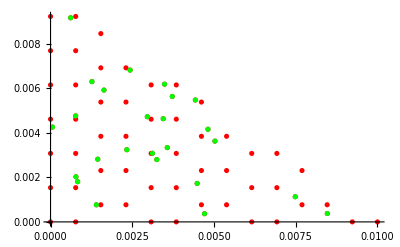

```mathematica
ListPlot[{Union[tDatGS[[1]],tDatGS[[-1]]],startDat},PlotStyle->{Red,Green}]
```

```mathematica
(* runs fine *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatGS
```

```mathematica
RandomSeed[1997];
pts=RandomPoint[ch,1000];
```

```mathematica
ensembleClf[clfs_,data_]:=Module[{decs,tfCounts},
decs=Thread[Map[#[data]&,clfs]];
tfCounts=Table[{Length[Select[decs[[j]],#==True&]],Length[Select[decs[[j]],#==False&]]},{j,1,Length[decs]}] ;(* {True counts, False counts} *)
Map[Which[
#[[1]]>#[[2]],True,
#[[1]]<#[[2]],False,
#[[1]]==#[[2]],RandomChoice[{1/2,1/2}->{True,False}]
]&,tfCounts]
]
```

```mathematica
ListPlot[{Select[Thread[{pts,ensembleClf[Flatten[gsClfs],pts]}],Last[#]==True&][[All,1]],Select[Thread[{pts,ensembleClf[Flatten[gsClfs],pts]}],Last[#]==False&][[All,1]]},PlotStyle->{Red,Black}];
```

```mathematica
Show[Plot3D[{gsClfs[[1]][[60]][{x,y},"Probability"->True],gsClfs[[1]][[60]][{x,y},"Probability"->False]},{x,0,0.01},{y,0,0.01},Exclusions->None],ListPointPlot3D[Map[Append[#,1]&,{Select[Normal[Join[startDat,pool]],pbI2Precipitates[#]&],Select[Normal[Join[startDat,pool]],Not[pbI2Precipitates[#]]&]},{2}],PlotStyle->{Red,Black}]];
```

```mathematica
Show[Plot3D[{Mean[#[{x,y},"Probability"->True]&/@gsClfs[[1]]],Mean[#[{x,y},"Probability"->False]&/@gsClfs[[1]]]},{x,0,0.01},{y,0,0.01},Exclusions->None],ListPointPlot3D[Map[Append[#,1]&,{Select[Normal[Join[startDat,pool]],pbI2Precipitates[#]&],Select[Normal[Join[startDat,pool]],Not[pbI2Precipitates[#]]&]},{2}],PlotStyle->{Red,Black}]]
```

-Graphics3D-

#### RD

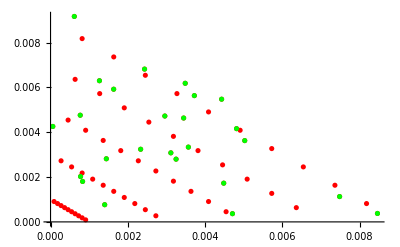

```mathematica
ListPlot[{Union[tDatRD[[1]],tDatRD[[-1]]],startDat},PlotStyle->{Red,Green}]
```

```mathematica
(* runs fine *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatRD;
```

#### RA

```mathematica
ListPlot[{Union[tDatRA[[1]],tDatRA[[-1]]],startDat},PlotStyle->{Red,Green}];
```

```mathematica
(* runs too slow *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatRA;
```

#### U

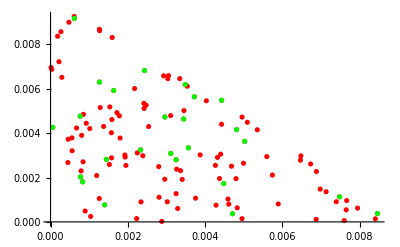

```mathematica
ListPlot[{Union[tDatU[[1]],tDatU[[-1]]],Normal[startDat]},PlotStyle->{Red,Green}]
```

```mathematica
(* runs fine *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatU
```

#### QBC

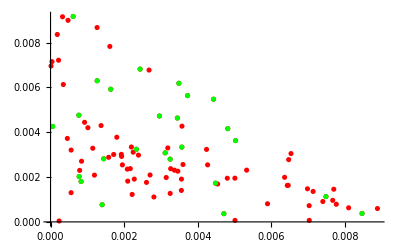

```mathematica
ListPlot[{Union[tDatQBC[[1]],tDatQBC[[-1]]],startDat},PlotStyle->{Red,Green}]
```

```mathematica
(* runs fine *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatQBC
```

```mathematica
Show[Plot3D[{clfsQBC[[-1]][{x,y},"Probability"->True],clfsQBC[[-1]][{x,y},"Probability"->False]},{x,0,0.01},{y,0,0.01},Exclusions->None],PlotStyle->{Red,Black}];
```

#### LTS

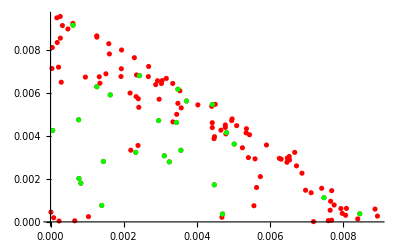

```mathematica
ListPlot[{Union[tDatLTS[[1]],tDatLTS[[-1]]],startDat},PlotStyle->{Red,Green}]
```

```mathematica
(* runs too slow *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatLTS;
```

#### LTSR

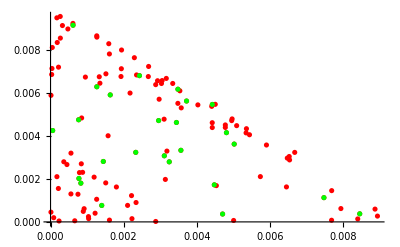

```mathematica
ListPlot[{Union[tDatLTSR[[1]],tDatLTSR[[-1]]],startDat},PlotStyle->{Red,Green}]
```

```mathematica
(* runs too slow *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatLTSR;
```

#### LTSNN

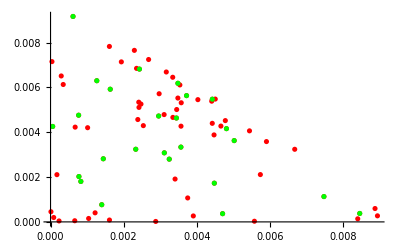

```mathematica
ListPlot[{Union[tDatLTSNN[[1]],tDatLTSNN[[-1]]],startDat},PlotStyle->{Red,Green}]
```

```mathematica
(* runs fine *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatLTSNN
```

#### Combined

```mathematica
Table[TTest[Mean[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]&/@{{gsRes,rdRes,raRes,uRes,ltsRes,ltsrRes,ltsnnRes}[[i]],qbcRes},Automatic,"TestDataTable"],{i,1,7}]
```

{ | Statistic | P-Value
T | -12.2942 | 2.16799×10^-24, | Statistic | P-Value
T | -16.1561 | 3.13343×10^-35, | Statistic | P-Value
T | -9.10799 | 5.26344×10^-16, | Statistic | P-Value
T | -6.41629 | 2.18578×10^-9, | Statistic | P-Value
T | -11.161 | 9.27918×10^-21, | Statistic | P-Value
T | -9.3282 | 2.51968×10^-16, | Statistic | P-Value
T | -19.3438 | 8.59951×10^-43}

```mathematica
Table[PairedTTest[Mean[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]&/@{{gsRes,rdRes,raRes,uRes,ltsRes,ltsrRes,ltsnnRes}[[i]],qbcRes},Automatic,"TestDataTable"],{i,1,7}]
```

{ | Statistic | P-Value
Paired T | -12.5391 | 3.65809×10^-22, | Statistic | P-Value
Paired T | -16.5082 | 3.4566×10^-30, | Statistic | P-Value
Paired T | -9.35991 | 2.7251×10^-15, | Statistic | P-Value
Paired T | -6.52753 | 2.87964×10^-9, | Statistic | P-Value
Paired T | -11.8849 | 9.04394×10^-21, | Statistic | P-Value
Paired T | -9.46894 | 1.57629×10^-15, | Statistic | P-Value
Paired T | -17.7397 | 1.65669×10^-32}

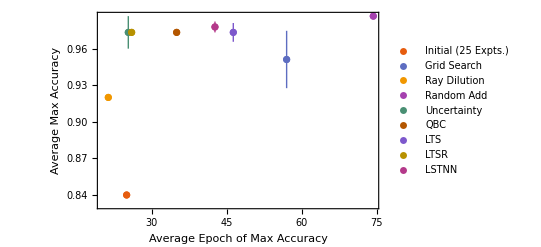

```mathematica
ListPlot[Partition[Prepend[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{gsRes,rdRes,raRes,uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},{Length@startDat,clfInitMeas["Accuracy"]}],1],PlotLegends->{"Initial (25 Expts.)","Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LSTNN"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full]
```

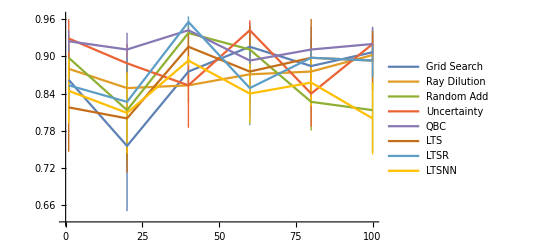

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{gsRes,rdRes,raRes,uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

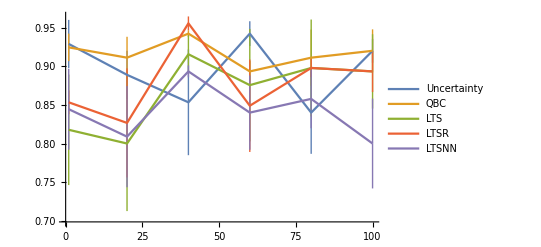

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},PlotLegends->{"Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

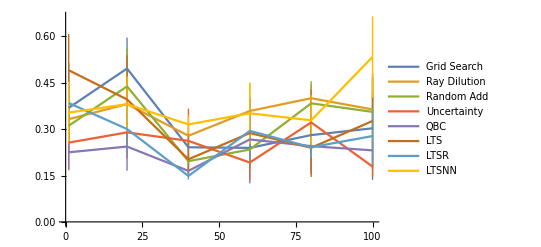

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"MeanCrossEntropy"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{gsRes,rdRes,raRes,uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

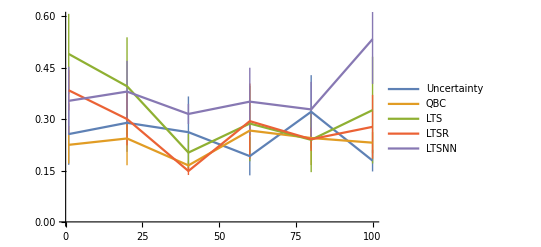

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"MeanCrossEntropy"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},PlotLegends->{"Uncertainty","QBC","LTS","LTSR","LTSNN"},PlotRange->{{0,100},{0,0.6}}]
```

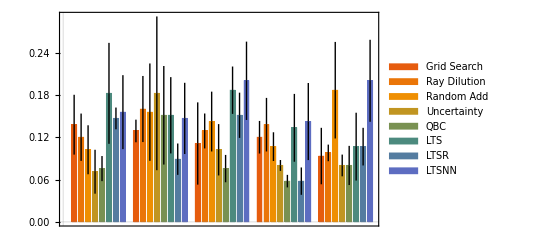

```mathematica
BarChart[Thread[MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Error"]],{j,1,Length[#]}]][[Prepend[Range[25,100,25],1]]]&/@{gsRes,rdRes,raRes,uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes}],PlotTheme->"Scientific",ChartLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

```mathematica
gsRes[[1]]//First//Keys//Normal
```

{Accuracy,AccuracyBaseline,AreaUnderROCCurve,BatchEvaluationTime,BestClassifiedExamples,CalibrationData,ClassifierFunction,ClassMeanCrossEntropy,ClassRejectionRate,CohenKappa,ConfusionDistribution,ConfusionFunction,ConfusionMatrix,DecisionUtilities,Error,F1Score,FalseDiscoveryRate,FalseNegativeNumber,FalseNegativeRate,FalsePositiveNumber,FalsePositiveRate,GeometricMeanProbability,LeastCertainExamples,Likelihood,LogLikelihood,MatthewsCorrelationCoefficient,MeanCrossEntropy,MeanDecisionUtility,NegativePredictiveValue,Perplexity,Precision,Recall,RejectionRate,ScottPi,Specificity,TopConfusions,TrueNegativeNumber,TruePositiveNumber}

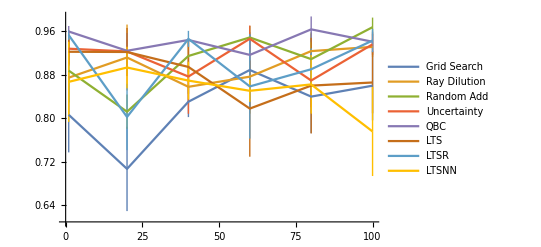

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#[[All,1]]]&/@Thread[Table[Normal[#[[j]][All,"Precision"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{gsRes,rdRes,raRes,uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

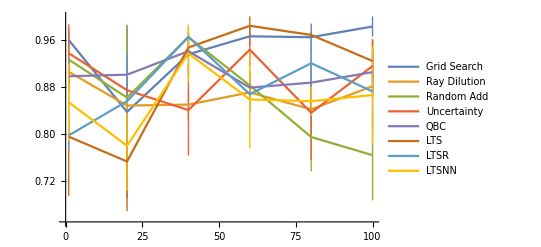

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#[[All,2]]]&/@Thread[Table[Normal[#[[j]][All,"Precision"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{gsRes,rdRes,raRes,uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

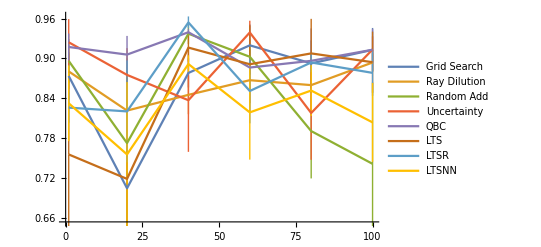

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#[[All,1]]]&/@Thread[Table[Normal[#[[j]][All,"F1Score"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{gsRes,rdRes,raRes,uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

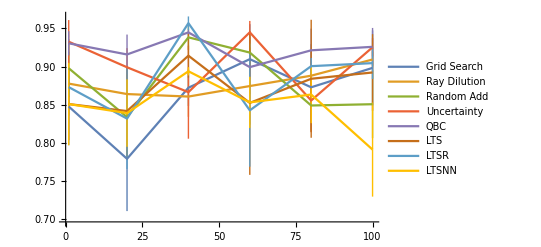

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#[[All,2]]]&/@Thread[Table[Normal[#[[j]][All,"F1Score"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{gsRes,rdRes,raRes,uRes,qbcRes,ltsRes,ltsrRes,ltsnnRes},PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

### Noiseless, starting from 5

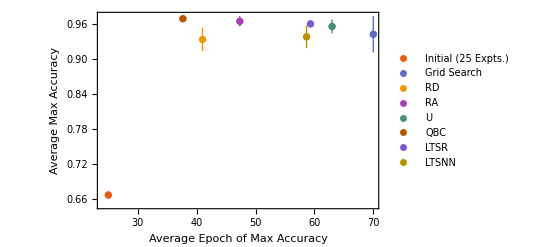

```mathematica
ListPlot[Partition[Prepend[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{gs5Res,rd5Res,ra5Res,u5Res,qbc5Res,ltsr5Res,ltsnn5Res},{Length@startDat,clfInit5Meas["Accuracy"]}],1],PlotLegends->{"Initial (25 Expts.)","Grid Search","RD","RA","U","QBC","LTSR","LTSNN"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full]
```

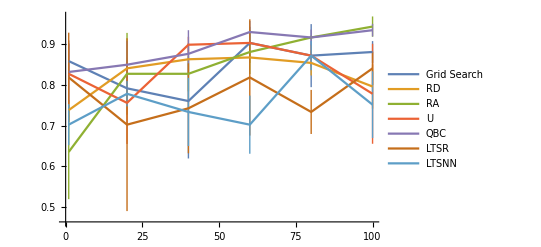

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{gs5Res,rd5Res,ra5Res,u5Res,qbc5Res,ltsr5Res,ltsnn5Res},PlotLegends->{"Grid Search","RD","RA","U","QBC","LTSR","LTSNN"}]
```

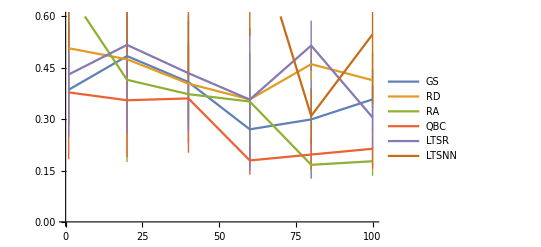

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"MeanCrossEntropy"]],{j,1,Length[#]}]]}][[Prepend[Range[20,100,20],1]]]&/@{gs5Res,rd5Res,ra5Res,qbc5Res,ltsr5Res,ltsnn5Res},PlotLegends->{"GS","RD","RA","QBC","LTSR","LTSNN"},PlotRange->{{0,100},{0,0.6}}]
```

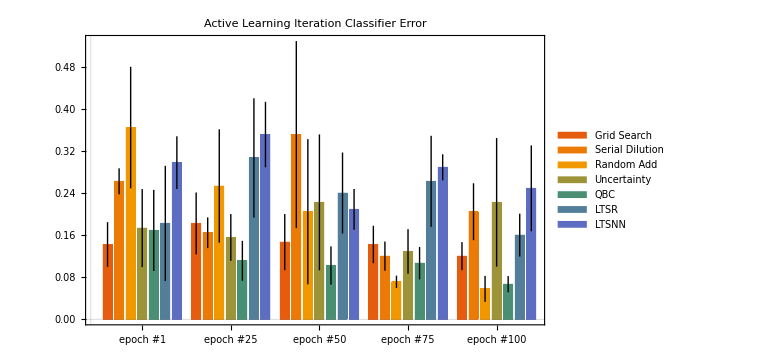

```mathematica
BarChart[Thread[MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Error"]],{j,1,Length[#]}]][[Prepend[Range[25,100,25],1]]]&/@{gs5Res,rd5Res,ra5Res,u5Res,qbc5Res,ltsr5Res,ltsnn5Res}],PlotTheme->"Scientific",ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTSR","LTSNN"},{0.9,0.8}],PlotLabel->"Active Learning Iteration Classifier Error",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Large,LabelStyle->Black]
```

### Noise

#### Grid Search

```mathematica
(* grid search change with noise *)
```

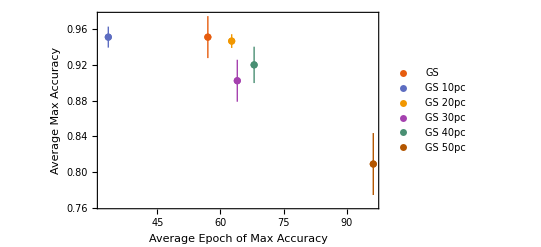

```mathematica
ListPlot[Partition[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{gsRes,gs10pcRes,gs20pcRes,gs30pcRes,gs40pcRes,gs50pcRes},1],PlotLegends->{"GS","GS 10pc","GS 20pc","GS 30pc","GS 40pc","GS 50pc"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full];
```

```mathematica
(* grid search change with noise *)
```

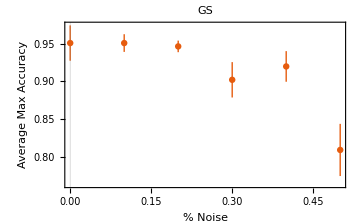

```mathematica
gsnPlt=ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{gsRes,gs10pcRes,gs20pcRes,gs30pcRes,gs40pcRes,gs50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLabel->"GS",ImageSize->Medium]
```

```mathematica
Fit[Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{gsRes,gs10pcRes,gs20pcRes,gs30pcRes,gs40pcRes,gs50pcRes}}],{1,x,x^2},x]
```

0.94619+0.174127 x-0.833333 x^2

```mathematica
Fit[Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{gsRes,gs10pcRes,gs20pcRes,gs30pcRes,gs40pcRes,gs50pcRes}}],{1,x},x]
```

0.973968-0.24254 x

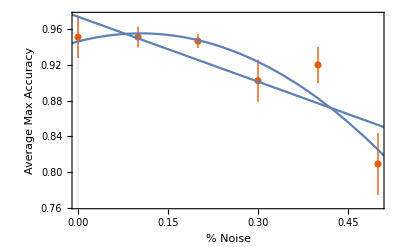

```mathematica
Show[ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{gsRes,gs10pcRes,gs20pcRes,gs30pcRes,gs40pcRes,gs50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full],Plot[0.9461904761904766+0.1741269841269827 x-0.8333333333333279 x^2,{x,-2.5056141199482354,2.714566500900616}],Plot[0.9739682539682541-0.24253968253968378 x,{x,-6.023560209424054,6.023560209424054}]]
```

#### Ray Dilution

```mathematica
(* ray dilution change with noise *)
```

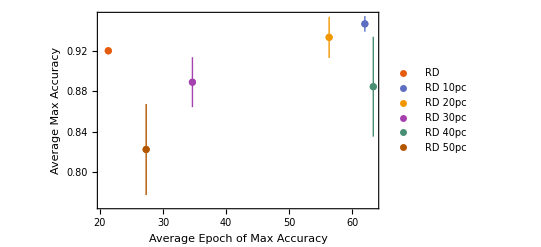

```mathematica
ListPlot[Partition[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{rdRes,rd10pcRes,rd20pcRes,rd30pcRes,rd40pcRes,rd50pcRes},1],PlotLegends->{"RD","RD 10pc","RD 20pc","RD 30pc","RD 40pc","RD 50pc"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full];
```

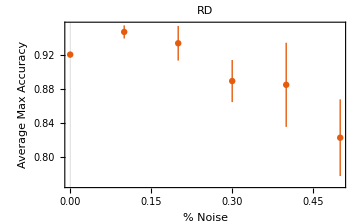

```mathematica
rdnPlt=ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{rdRes,rd10pcRes,rd20pcRes,rd30pcRes,rd40pcRes,rd50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLabel->"RD",ImageSize->Medium]
```

#### Random Add

```mathematica
(* random add change with noise *)
```

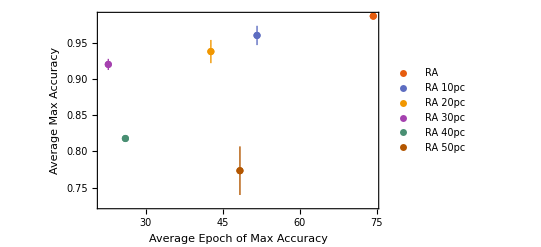

```mathematica
ListPlot[Partition[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{raRes,ra10pcRes,ra20pcRes,ra30pcRes,ra40pcRes,ra50pcRes},1],PlotLegends->{"RA","RA 10pc","RA 20pc","RA 30pc","RA 40pc","RA 50pc"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full];
```

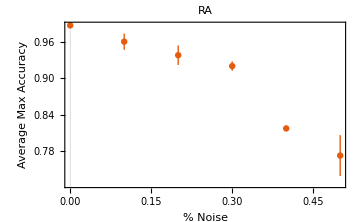

```mathematica
ranPlt=ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{raRes,ra10pcRes,ra20pcRes,ra30pcRes,ra40pcRes,ra50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLabel->"RA",ImageSize->Medium]
```

#### Uncertainty

```mathematica
(* random add change with noise *)
```

```mathematica
ListPlot[Partition[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{uRes,u10pcRes,u20pcRes,u30pcRes,u40pcRes,u50pcRes},1],PlotLegends->{"U","U 10pc","U 20pc","U 30pc","U 40pc","U 50pc"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full];
```

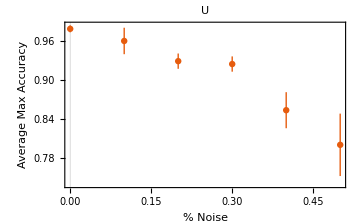

```mathematica
unPlt=ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{uRes,u10pcRes,u20pcRes,u30pcRes,u40pcRes,u50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLabel->"U",ImageSize->Medium]
```

```mathematica
Fit[Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{uRes,u10pcRes,u20pcRes,u30pcRes,u40pcRes,u50pcRes}}],{1,x,x^2},x]
```

0.974698-0.0503175 x-0.595238 x^2

```mathematica
Fit[Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{uRes,u10pcRes,u20pcRes,u30pcRes,u40pcRes,u50pcRes}}],{1,x},x]
```

0.99454-0.347937 x

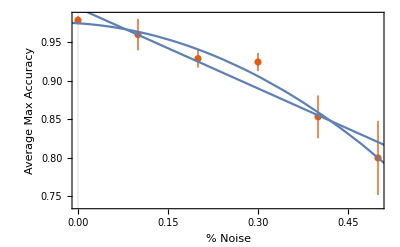

```mathematica
Show[ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{uRes,u10pcRes,u20pcRes,u30pcRes,u40pcRes,u50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full],Plot[0.9746984126984128-0.05031746031746037 x-0.5952380952380922 x^2,{x,-3.1767458897594043,3.0922125564260705}],Plot[0.9945396825396826-0.34793650793650865 x,{x,-4.287591240875904,4.287591240875904}]]
```

#### Query by Committee

```mathematica
(* random add change with noise *)
```

```mathematica
ListPlot[Partition[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{qbcRes,qbc10pcRes,qbc20pcRes,qbc30pcRes,qbc40pcRes,qbc50pcRes},1],PlotLegends->{"QBC","QBC 10pc","QBC 20pc","QBC 30pc","QBC 40pc","QBC 50pc"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full];
```

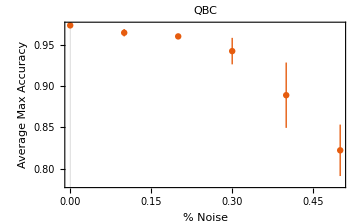

```mathematica
qbcPlt=ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{qbcRes,qbc10pcRes,qbc20pcRes,qbc30pcRes,qbc40pcRes,qbc50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLabel->"QBC",ImageSize->Medium]
```

#### LTS

```mathematica
(* random add change with noise *)
```

```mathematica
ListPlot[Partition[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{ltsRes,lts10pcRes,lts20pcRes,lts30pcRes,lts40pcRes,lts50pcRes},1],PlotLegends->{"LTS","LTS 10pc","LTS 20pc","LTS 30pc","LTS 40pc","LTS 50pc"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full];
```

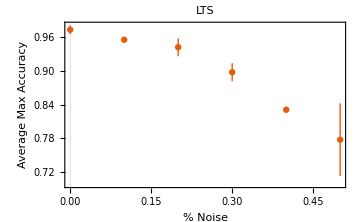

```mathematica
ltsPlt=ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{ltsRes,lts10pcRes,lts20pcRes,lts30pcRes,lts40pcRes,lts50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLabel->"LTS",ImageSize->Medium]
```

#### LTSR

```mathematica
(* random add change with noise *)
```

```mathematica
ListPlot[Partition[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{ltsrRes,ltsr10pcRes,ltsr20pcRes,ltsr30pcRes,ltsr40pcRes,ltsr50pcRes},1],PlotLegends->{"LTSR","LTSR 10pc","LTSR 20pc","LTSR 30pc","LTSR 40pc","LTSR 50pc"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full];
```

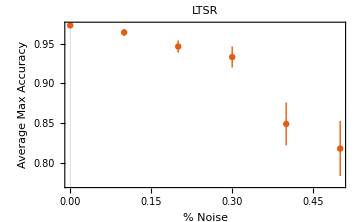

```mathematica
ltsrPlt=ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{ltsrRes,ltsr10pcRes,ltsr20pcRes,ltsr30pcRes,ltsr40pcRes,ltsr50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLabel->"LTSR",ImageSize->Medium]
```

#### LTSNN

```mathematica
(* random add change with noise *)
```

```mathematica
ListPlot[Partition[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{ltsnnRes,ltsnn10pcRes,ltsnn20pcRes,ltsnn30pcRes,ltsnn40pcRes,ltsnn50pcRes},1],PlotLegends->{"LTSNN","LTSNN 10pc","LTSNN 20pc","LTSNN 30pc","LTSNN 40pc","LTSNN 50pc"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full];
```

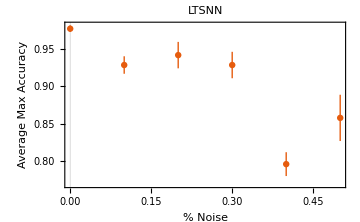

```mathematica
ltsnnPlt=ListPlot[Thread[{Range[0,5]/10,MeanAround[maxAcc[#]]&/@{ltsnnRes,ltsnn10pcRes,ltsnn20pcRes,ltsnn30pcRes,ltsnn40pcRes,ltsnn50pcRes}}],PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLabel->"LTSNN",ImageSize->Medium]
```

#### Combined

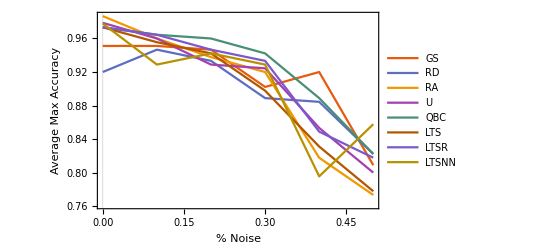

```mathematica
ListLinePlot[{Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{gsRes,gs10pcRes,gs20pcRes,gs30pcRes,gs40pcRes,gs50pcRes}}],Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{rdRes,rd10pcRes,rd20pcRes,rd30pcRes,rd40pcRes,rd50pcRes}}],Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{raRes,ra10pcRes,ra20pcRes,ra30pcRes,ra40pcRes,ra50pcRes}}],Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{uRes,u10pcRes,u20pcRes,u30pcRes,u40pcRes,u50pcRes}}],
Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{qbcRes,qbc10pcRes,qbc20pcRes,qbc30pcRes,qbc40pcRes,qbc50pcRes}}],
Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{ltsRes,lts10pcRes,lts20pcRes,lts30pcRes,lts40pcRes,lts50pcRes}}],
Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{ltsrRes,ltsr10pcRes,ltsr20pcRes,ltsr30pcRes,ltsr40pcRes,ltsr50pcRes}}],
Thread[{Range[0,5]/10,Mean[maxAcc[#]]&/@{ltsnnRes,ltsnn10pcRes,ltsnn20pcRes,ltsnn30pcRes,ltsnn40pcRes,ltsnn50pcRes}}]},PlotTheme->"Scientific",FrameLabel->{"% Noise","Average Max Accuracy"},PlotRange->Full,PlotLegends->{"GS","RD","RA","U","QBC","LTS","LTSR","LTSNN"}]
```

```mathematica
noiseRes={{gs10pcRes,rd10pcRes,ra10pcRes,u10pcRes,qbc10pcRes,lts10pcRes,ltsr10pcRes,ltsnn10pcRes},{gs20pcRes,rd20pcRes,ra20pcRes,u20pcRes,qbc20pcRes,lts20pcRes,ltsr20pcRes,ltsnn20pcRes},{gs30pcRes,rd30pcRes,ra30pcRes,u30pcRes,qbc30pcRes,lts30pcRes,ltsr30pcRes,ltsnn30pcRes},{gs50pcRes,rd40pcRes,ra40pcRes,u40pcRes,qbc40pcRes,lts40pcRes,ltsr40pcRes,ltsnn40pcRes},{gs50pcRes,rd50pcRes,ra50pcRes,u50pcRes,qbc50pcRes,lts50pcRes,ltsr50pcRes,ltsnn50pcRes}};
```

```mathematica
clfinitpcMeas={clfInit10pcMeas,clfInit20pcMeas,clfInit30pcMeas,clfInit40pcMeas,clfInit50pcMeas};
```

```mathematica
(* downsampled accuracy vs epoch for diff noise levels *)
```

```mathematica
Manipulate[ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Range[1,100,20]]]&/@noiseRes[[a]],PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}],{a,{1,2,3,4,5}}];
```

```mathematica
(* downsampled mean max acc. vs. mean pos. where acc. was achieved for diff noise levels *)
```

```mathematica
Manipulate[Quiet@ListPlot[Partition[Prepend[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@noiseRes[[a]],{Length@startDat,clfinitpcMeas[[a]]["Accuracy"]}],1],PlotLegends->{"Initial (25 Expts.)","Grid Search","Ray Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LSTNN"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full],{a,{1,2,3,4,5}}];
```

### Imbalanced

#### GS

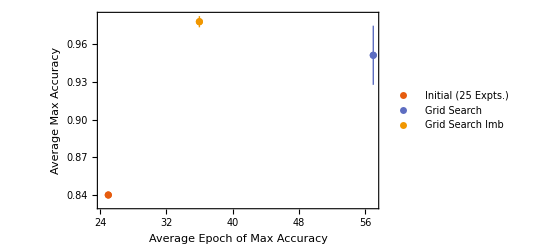

```mathematica
ListPlot[Partition[Prepend[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{gsRes,gsImbRes},{Length@startDat,clfInitMeas["Accuracy"]}],1],PlotLegends->{"Initial (25 Expts.)","Grid Search","Grid Search Imb"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full]
```

```mathematica
ListPlot[{Union[tDatGSImb[[1]],tDatGSImb[[-1]]],startDat},PlotStyle->{Red,Green}]
```

-Graphics-

```mathematica
(* runs fine *)
```

```mathematica
Animate[ListPlot[Table[{Union[#[[1]],#[[a]]],Normal[startDat]},{a,1,Length[#]}][[m]],PlotStyle->{Red,Green}],{m,Range[1,Length[#]]}]&@tDatGSImb;
```

#### Combined

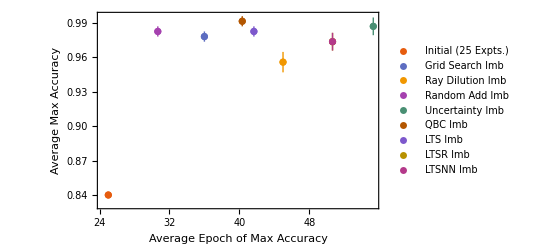

```mathematica
ListPlot[Partition[Prepend[{Mean[maxAccPos[#]],MeanAround[maxAcc[#]]}&/@{gsImbRes,rdImbRes,raImbRes,uImbRes,qbcImbRes,ltsImbRes,ltsrImbRes,ltsnnImbRes},{Length@startDat,clfInitMeas["Accuracy"]}],1],PlotLegends->{"Initial (25 Expts.)","Grid Search Imb","Ray Dilution Imb","Random Add Imb","Uncertainty Imb","QBC Imb","LTS Imb","LTSR Imb","LTSNN Imb"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full]
```

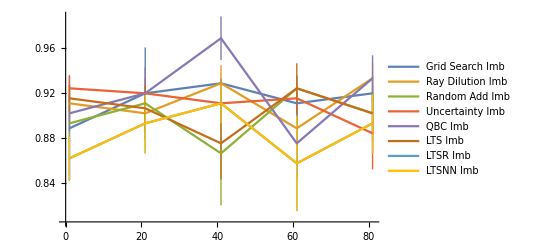

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Range[1,100,20]]]&/@{gsImbRes,rdImbRes,raImbRes,uImbRes,qbcImbRes,ltsImbRes,ltsrImbRes,ltsnnImbRes},PlotLegends->{"Grid Search Imb","Ray Dilution Imb","Random Add Imb","Uncertainty Imb","QBC Imb","LTS Imb","LTSR Imb","LTSNN Imb"}]
```

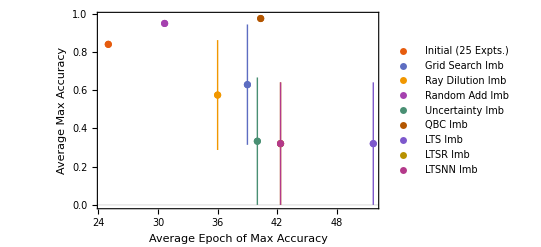

```mathematica
ListPlot[Partition[Prepend[{Mean[maxMCCPos[#]],MeanAround[maxMCC[#]]}&/@{gsImbRes,rdImbRes,raImbRes,uImbRes,qbcImbRes,ltsImbRes,ltsrImbRes,ltsnnImbRes},{Length@startDat,clfInitMeas["Accuracy"]}],1],PlotLegends->{"Initial (25 Expts.)","Grid Search Imb","Ray Dilution Imb","Random Add Imb","Uncertainty Imb","QBC Imb","LTS Imb","LTSR Imb","LTSNN Imb"},PlotTheme->"Scientific",FrameLabel->{"Average Epoch of Max Accuracy","Average Max Accuracy"},PlotRange->Full]
```

## Figures - 2D

### Set-up related

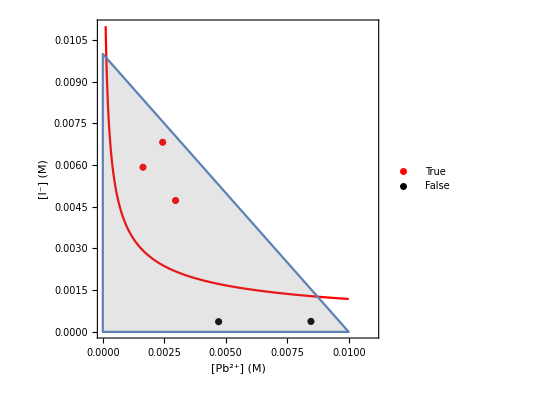

```mathematica
sdPlot2D=Show[Plot[Sqrt[Ksp/Pb],{Pb,10^-5,0.01},PlotRange->{{0,0.011},{0,0.011}},PlotStyle->Red,AspectRatio->1,Frame->True,FrameLabel->{"[Pb^(2+)] (M)","[I^-] (M)"}],ListPlot[{Select[Thread[{Normal[startDat5],pbI2Precipitates/@Normal[startDat5]}],Last[#]&][[All,1]],Select[Thread[{Normal[startDat5],pbI2Precipitates/@Normal[startDat5]}],Not@Last[#]&][[All,1]]},PlotStyle->{Red,Black},PlotLegends->Placed[{"True","False"},{0.9,0.9}]],
RegionPlot[ch,PlotStyle->{Gray,Opacity[0.2]}],LabelStyle->Black]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\stDatPlot2D.pdf",sdPlot2D,"PDF"];
```

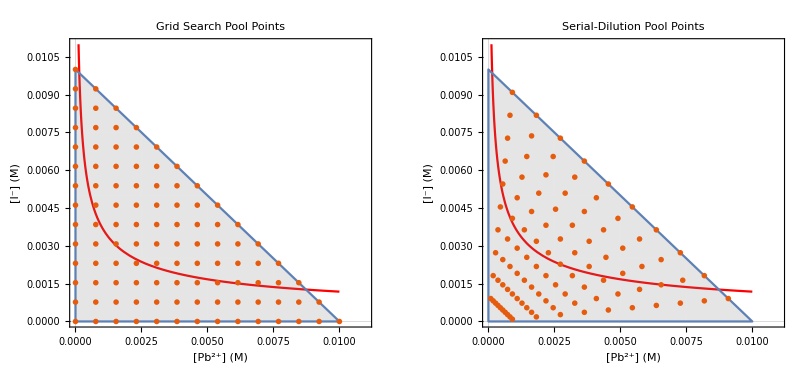

```mathematica
gsAndRDPlt=GraphicsRow[{Show[Plot[Sqrt[Ksp/Pb],{Pb,10^-5,0.01},PlotRange->{{0,0.011},{0,0.011}},PlotStyle->Red,AspectRatio->1,Frame->True,FrameLabel->{"[Pb^(2+)] (M)","[I^-] (M)"},LabelStyle->Black,PlotTheme->"Scientific",PlotStyle->Black],RegionPlot[ch,PlotStyle->{Gray,Opacity[0.2]}],ListPlot[gstGrid,PlotTheme->"Scientific",PlotMarkers->{"●",Scaled[0.02]}],PlotLabel->"Grid Search Pool Points",ImageSize->Large],Show[Plot[Sqrt[Ksp/Pb],{Pb,10^-5,0.01},PlotRange->{{0,0.011},{0,0.011}},PlotStyle->Red,AspectRatio->1,Frame->True,FrameLabel->{"[Pb^(2+)] (M)","[I^-] (M)"},LabelStyle->Black,PlotTheme->"Scientific",PlotStyle->Black],RegionPlot[ch,PlotStyle->{Gray,Opacity[0.2]}],ListPlot[Flatten[rayPts,1],PlotMarkers->{"●",Scaled[0.02]},PlotTheme->"Scientific"],PlotLabel->"Serial-Dilution Pool Points",ImageSize->Large]},LabelStyle->Black]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\gsAndRDPlot2D.pdf",gsAndRDPlt,"PDF"];
```

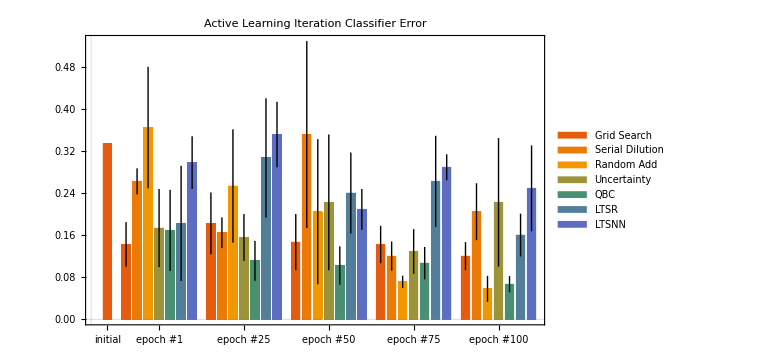

```mathematica
res52DErrorplt=BarChart[Prepend[Thread[MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Error"]],{j,1,Length[#]}]][[Prepend[Range[25,100,25],1]]]&/@{gs5Res,rd5Res,ra5Res,u5Res,qbc5Res,ltsr5Res,ltsnn5Res}],{clfInit5Meas["Error"]}],PlotTheme->"Scientific",ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTSR","LTSNN"},{0.9,0.8}],PlotLabel->"Active Learning Iteration Classifier Error",ChartLabels->{{"initial","epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Large,LabelStyle->Black]
```

```mathematica
Cases[res52DErrorplt,RGBColor[x_,y_,z_]:>{x,y,z},Infinity]
```

{{0.9,0.36,0.054},{0.9,0.36,0.054},{0.922554,0.476951,0.027},{0.945109,0.593901,0.},{0.615465,0.576951,0.225387},{0.285821,0.56,0.450773},{0.325535,0.493901,0.604535},{0.365248,0.427802,0.758297},{0.9,0.36,0.054},{0.922554,0.476951,0.027},{0.945109,0.593901,0.},{0.615465,0.576951,0.225387},{0.285821,0.56,0.450773},{0.325535,0.493901,0.604535},{0.365248,0.427802,0.758297},{0.9,0.36,0.054},{0.922554,0.476951,0.027},{0.945109,0.593901,0.},{0.615465,0.576951,0.225387},{0.285821,0.56,0.450773},{0.325535,0.493901,0.604535},{0.365248,0.427802,0.758297},{0.9,0.36,0.054},{0.922554,0.476951,0.027},{0.945109,0.593901,0.},{0.615465,0.576951,0.225387},{0.285821,0.56,0.450773},{0.325535,0.493901,0.604535},{0.365248,0.427802,0.758297},{0.9,0.36,0.054},{0.922554,0.476951,0.027},{0.945109,0.593901,0.},{0.615465,0.576951,0.225387},{0.285821,0.56,0.450773},{0.325535,0.493901,0.604535},{0.365248,0.427802,0.758297},{0.9,0.36,0.054},{0.922554,0.476951,0.027},{0.945109,0.593901,0.},{0.615465,0.576951,0.225387},{0.285821,0.56,0.450773},{0.325535,0.493901,0.604535},{0.365248,0.427802,0.758297}}

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\res52DErrorplt.pdf",res52DErrorplt,"PDF"];
```

```mathematica
BarChart[Prepend[Thread[MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]][[Prepend[Range[25,100,25],1]]]&/@{gs5Res,rd5Res,ra5Res,u5Res,qbc5Res,ltsr5Res,ltsnn5Res}],{clfInit5Meas["Accuracy"]}],PlotTheme->"Scientific",ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTSR","LTSNN"},{1.,0.75}],PlotLabel->"Active Learning Iteration Classifier Accuracy",ChartLabels->{{"initial","epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Large,LabelStyle->Black]
```

-Graphics-

```mathematica
BarChart[Prepend[Thread[MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"MeanCrossEntropy"]],{j,1,Length[#]}]][[Prepend[Range[25,100,25],1]]]&/@{gs5Res,rd5Res,ra5Res,u5Res,qbc5Res,ltsr5Res,ltsnn5Res}],{clfInit5Meas["MeanCrossEntropy"]}],PlotTheme->"Scientific",ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTSR","LTSNN"},{1.,0.75}],PlotLabel->"Active Learning Iteration Classifier Error",ChartLabels->{{"initial","epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Large,LabelStyle->Black]
```

-Graphics-

### Noiseless

```mathematica
(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
plotColors={RGBColor[0.9, 0.36, 0.054],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.365248, 0.427802, 0.758297]};
```

```mathematica
SwatchLegend[plotColors,{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]
```

```mathematica
barDatAcc2D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatAcc2D.txt"]];
```

```mathematica
barDatAcc2Drerun=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatACC2DRERUN.txt"]];
```

```mathematica
barDatError2D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatError2D.txt"]];
```

```mathematica
Thread[{SetPrecision[Thread[barDatAcc2D][[5]],3],SetPrecision[Thread[barDatError2D][[5]],3]}]
```

{{0.96,0.04},{0.933,0.0667},{0.973,0.0267},{0.96,0.04},{0.933,0.0667},{0.947,0.0533},{0.947,0.0533},{0.973,0.0267}}

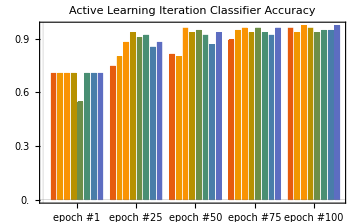

```mathematica
barAcc2D=BarChart[Thread[barDatAcc2D],PlotTheme->"Scientific"(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*),ChartStyle->plotColors,PlotLabel->"Active Learning Iteration Classifier Accuracy",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->Large,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

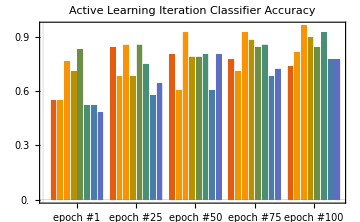

```mathematica
BarChart[Thread[barDatAcc2Drerun],PlotTheme->"Scientific"(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*),ChartStyle->plotColors,PlotLabel->"Active Learning Iteration Classifier Accuracy",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->Large,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

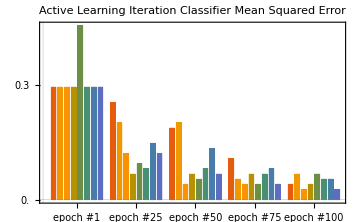

```mathematica
barError2D=BarChart[Thread[barDatError2D],PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Iteration Classifier Mean Squared Error",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

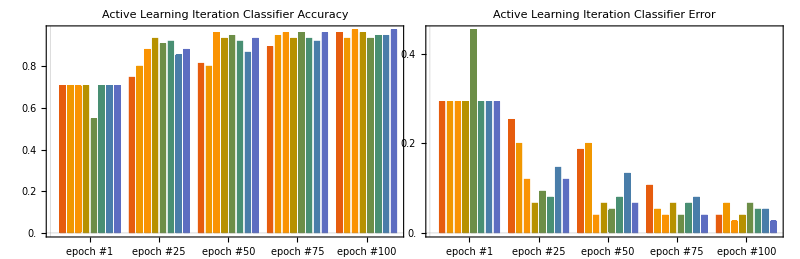

```mathematica
barAccError2D=GraphicsRow[{barAcc2D,barError2D,SwatchLegend[plotColors,{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]},ImageSize->Full,Spacings->-35]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\barAccError2D.pdf",barAccError2D,"PDF"];
```

### Imbalanced

```mathematica
barDatAccImb2D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatAccImb2D.txt"]];
```

```mathematica
barDatErrorImb2D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatErrorImb2D.txt"]];
```

```mathematica
barDatMCCImb2D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatMCCImb2D.txt"]];
```

```mathematica
ToString[#[[1]]]<>"/"<>ToString[#[[2]]]&/@Thread[{SetPrecision[Thread[barDatMCCImb2D][[3]],3],SetPrecision[Thread[barDatErrorImb2D][[3]],3]}]
```

{0.724/0.187,0.764/0.0800,0.762/0.0800,0.884/0.0800,0.884/0.0533,0.729/0.0533,0.846/0.0800,0.678/0.0800}

```mathematica
StringRiffle[ToString[#[[1]]]<>"/"<>ToString[#[[2]]]&/@Thread[{SetPrecision[barDatMCCImb2D[[8]],3],SetPrecision[barDatErrorImb2D[[8]],3]}]," & "]
```

0.456/0.320 & 0.584/0.120 & 0.678/0.0800 & 0.766/0.0800 & 0.929/0.0667

```mathematica
Thread[barDatMCCImb2D][[All,1]]
```

{0.456407,0.377037,0.724491,0.806139,0.884889}

```mathematica
Thread[barDatErrorImb2D][[All,1]]
```

{0.32,0.24,0.186667,0.146667,0.133333}

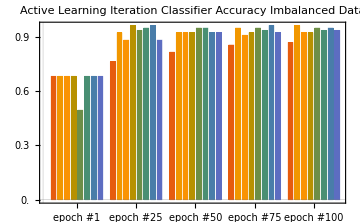

```mathematica
barAccImb2D=BarChart[Thread[barDatAccImb2D],PlotTheme->"Scientific"(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*),ChartStyle->plotColors,PlotLabel->"Active Learning Iteration Classifier Accuracy\nImbalanced Data",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->Large,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

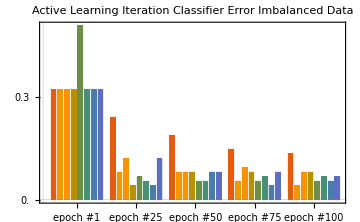

```mathematica
barErrorImb2D=BarChart[Thread[barDatErrorImb2D],PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Iteration Classifier Error\nImbalanced Data",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

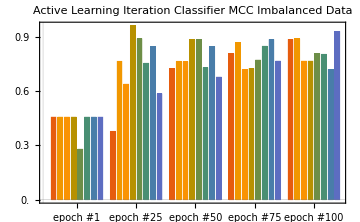

```mathematica
barMCCImb2D=BarChart[Thread[barDatMCCImb2D],PlotTheme->"Scientific"(*,ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}]*),ChartStyle->plotColors,PlotLabel->"Active Learning Iteration Classifier MCC\nImbalanced Data",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->Medium,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

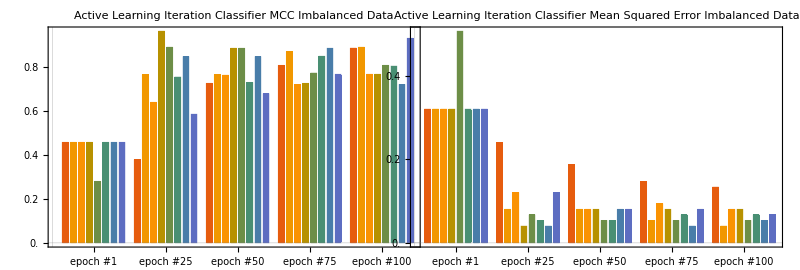

```mathematica
barMCCErrorImb2D=GraphicsRow[{barMCCImb2D,barErrorImb2D,SwatchLegend[plotColors,{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]},ImageSize->Full,Spacings->-62]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\barMCCErrorImb2D.pdf",barMCCErrorImb2D,"PDF"];
```

### Noise

```mathematica
accs25Noise=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\accs25Noise.txt"]];
```

```mathematica
accs75Noise=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\accs75Noise.txt"]];
```

```mathematica
accs100Noise=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\accs100Noise.txt"]];
```

```mathematica
StringRiffle[ToString[#[[1]]]<>"/"<>ToString[#[[2]]]&/@Thread[{SetPrecision[Thread[accs25Noise][[8]],3],SetPrecision[Thread[accs100Noise][[8]],3]}]," & "]
```

0.787/0.973 & 0.720/0.907 & 0.747/0.907 & 0.773/0.400 & 0.320/0.493

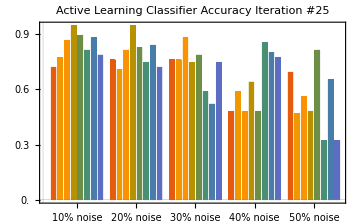

```mathematica
accs25NoiseBar=BarChart[accs25Noise,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier Accuracy\nIteration #25",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

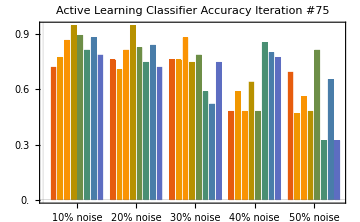

```mathematica
accs75NoiseBar=BarChart[accs25Noise,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier Accuracy\nIteration #75",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

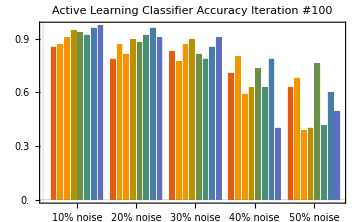

```mathematica
accs100NoiseBar=BarChart[accs100Noise,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier Accuracy\nIteration #100",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

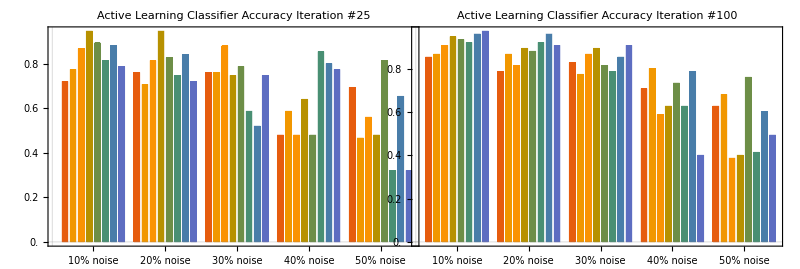

```mathematica
noiseAccs2DBar=GraphicsRow[{accs25NoiseBar,accs100NoiseBar,SwatchLegend[plotColors,{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]},ImageSize->Full,Spacings->-60]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\noiseAccs2Dbar.pdf",noiseAccs2DBar,"PDF"];
```

## Figures - 3D

```mathematica
plotColors={RGBColor[0.9, 0.36, 0.054],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.365248, 0.427802, 0.758297]};
```

### Set-up related

```mathematica
ch3D=ConvexHullMesh[{{0,0,0},{1,0,0},{0,1,0},{0,0,1}}];
```

```mathematica
k1=0.01;
k2=0.1;
```

```mathematica
acPpt[{a_,b_,c_},acKsp_:k1]:=(c>=acKsp/a)
```

```mathematica
acPpt[{a_,b_,c_},acKsp_:k1]:=If[a==0,False,(c>=acKsp/a)]
```

```mathematica
bcPpt[{a_,b_,c_},bcKsp_:k2]:=If[b==0,False,(c>=bcKsp/b)]
```

```mathematica
ptClfy[{a_,b_,c_}]:=Which[
acPpt[{a,b,c}]&&Not[bcPpt[{a,b,c}]],"ac",
Not[acPpt[{a,b,c}]],"none",
(acPpt[{a,b,c}]&&bcPpt[{a,b,c}]),"either"
]
```

```mathematica
allTrain3D=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\allTrainCont3D.csv"];
```

```mathematica
test3D=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\testCont3D.csv"];
```

```mathematica
startDat3D=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\startDatCont3D.csv"];
```

```mathematica
pool3D=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\poolCont3D.csv"];
```

```mathematica
pts//Length
```

350

```mathematica
pts=pts[[1;;100]];
```

```mathematica
setup3D=GraphicsRow[{Show[Plot3D[{k1/a,k2/b}, (*AC and BC equilibrium curves*)
{a,0,1},{b,0,1},
AxesLabel->{"[A]","[B]","[C]"},AspectRatio->1,BoxRatios->{1, 1, 1},PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->{Opacity[0.95],Blue,Opacity[0.95],Yellow}],HighlightMesh[ch3D,Style[2,Opacity[0.5]],ImageSize->Medium],ListPointPlot3D[{Select[pts,acPpt[#]&&Not[bcPpt[#]]&],Select[pts,Not@acPpt[#]&],Select[pts,acPpt[#]&&bcPpt[#]&]},PlotStyle->{Red,Black,Green}],ViewPoint->{3.3, -1.4, 2.}],SwatchLegend[{Yellow,Blue},{"K1","K2"}],PointLegend[{Black,Red,Green},{"No PPT.","AC PPT.","AC & BC PPT."}]},Spacings->-15]
```

-Graphics-

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\setup3D.pdf",setup3D,"PDF"];
```

### Noiseless

```mathematica
barDatAcc3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatAcc3D.txt"]];
```

```mathematica
barDatError3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatError3D.txt"]];
```

```mathematica
barDatMCC3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\barDatMCC3D.txt"]];
```

```mathematica
StringRiffle[ToString[#[[1]]]<>"/"<>ToString[#[[2]]]&/@Thread[{SetPrecision[barDatAcc3D[[8]],3],SetPrecision[ barDatError2D[[8]],3]}]," & "]
```

0.733/0.293 & 0.733/0.120 & 0.787/0.0667 & 0.867/0.0400 & 0.893/0.0267

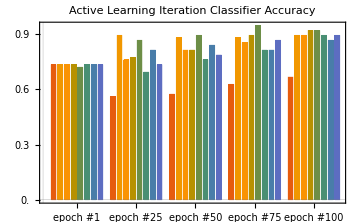

```mathematica
BarChart[Thread[barDatAcc3D2],PlotTheme->"Scientific"(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*),ChartStyle->plotColors,PlotLabel->"Active Learning Iteration Classifier Accuracy",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->Medium,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

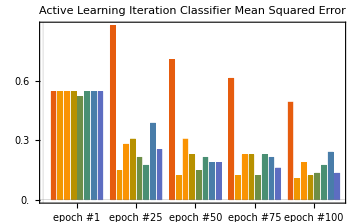

```mathematica
barError3D=BarChart[Thread[barDatError3D],PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Iteration Classifier Mean Squared Error",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->Medium,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

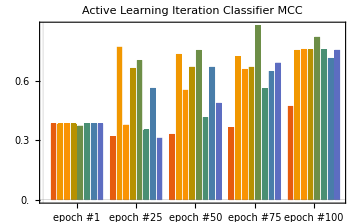

```mathematica
barMCC3D=BarChart[Thread[barDatMCC3D],PlotTheme->"Scientific"(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*),ChartStyle->plotColors,PlotLabel->"Active Learning Iteration Classifier MCC",ChartLabels->{{"epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->Medium,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

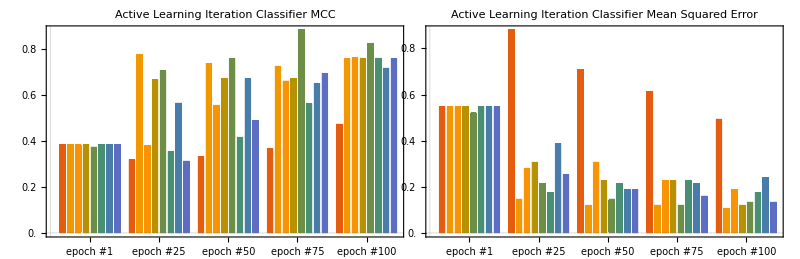

```mathematica
barMCCError3D=GraphicsRow[{barMCC3D,barError3D,SwatchLegend[plotColors,{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]},ImageSize->Full,Spacings->-35]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\barMCCError3D.pdf",barMCCError3D,"PDF"];
```

```mathematica
Length@pool3D
```

250

```mathematica
Counts[ptClfy/@Normal[pool3D]]
```

<|none→54,ac→159,either→37|>

### Noise

```mathematica
accs25Noise3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\accs25Noise3D.txt"]];
```

```mathematica
accs75Noise3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\accs75Noise3D.txt"]];
```

```mathematica
accs100Noise3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\accs100Noise3D.txt"]];
```

```mathematica
mccs25Noise3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\mccs25Noise3D.txt"]];
```

```mathematica
mccs75Noise3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\mccs75Noise3D.txt"]];
```

```mathematica
mccs100Noise3D=Normal[SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\activeLearning\\mccs100Noise3D.txt"]];
```

```mathematica
StringRiffle[ToString[#[[1]]]<>"/"<>ToString[#[[2]]]&/@Thread[{SetPrecision[Thread[mccs25Noise3D][[8]],3],SetPrecision[Thread[mccs100Noise3D][[8]],3]}]," & "]
```

0.697/0.733 & 0.394/0.686 & 0.484/0.520 & 0.216/0.437 & -0.264/0.0103

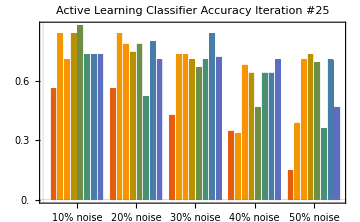

```mathematica
accs25NoiseBar3D=BarChart[accs25Noise3D,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier Accuracy\nIteration #25",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

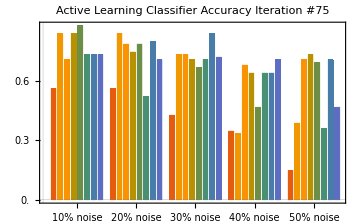

```mathematica
accs75NoiseBar3D=BarChart[accs25Noise3D,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier Accuracy\nIteration #75",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

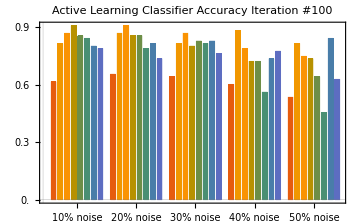

```mathematica
accs100NoiseBar3D=BarChart[accs100Noise3D,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier Accuracy\nIteration #100",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

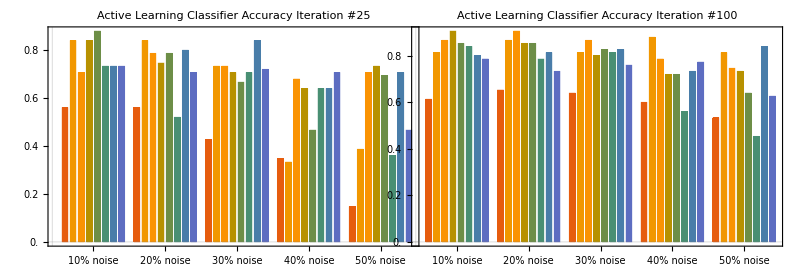

```mathematica
noiseAccs3DBar=GraphicsRow[{accs25NoiseBar3D,accs100NoiseBar3D,SwatchLegend[plotColors,{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]},ImageSize->Full,Spacings->-60]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\noiseAccs3Dbar.pdf",noiseAccs3DBar,"PDF"];
```

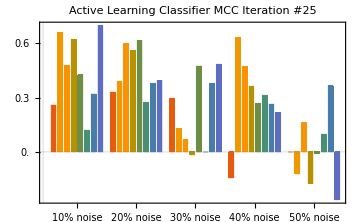

```mathematica
mccs25NoiseBar3D=BarChart[mccs25Noise3D,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier MCC\nIteration #25",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

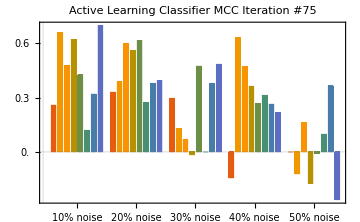

```mathematica
mccs75NoiseBar3D=BarChart[mccs25Noise3D,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier MCC\nIteration #75",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

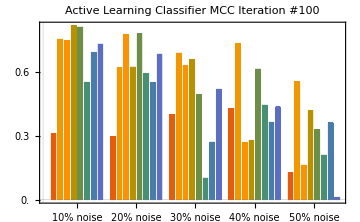

```mathematica
mccs100NoiseBar3D=BarChart[mccs100Noise3D,PlotTheme->"Scientific",ChartStyle->plotColors,(*ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"},{1,0.5}],*)PlotLabel->"Active Learning Classifier MCC\nIteration #100",ChartLabels->{{"10% noise","20% noise","30% noise","40% noise","50% noise"},None},ImageSize->Medium,LabelStyle->Black,ImageSize->15*15,FrameTicks->{{Range[0,1.0,0.1], None},{Automatic,None}}]
```

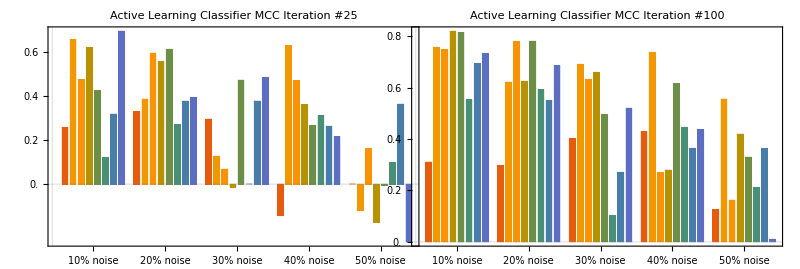

```mathematica
noiseMccs3DBar=GraphicsRow[{mccs25NoiseBar3D,mccs100NoiseBar3D,SwatchLegend[plotColors,{"Grid Search","Serial Dilution","Random Add","Uncertainty","QBC","LTS","LTSR","LTSNN"}]},ImageSize->Full,Spacings->-60]
```

```mathematica
Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\manuscript_draft\\noiseMccs3Dbar.pdf",noiseMccs3DBar,"PDF"];
```